```mathematica
MakeCycle[l_]:=Join[Table[l[[i]]<->l[[i+1]],{i,1,Length[l]-1}],{l[[Length[l]]]<->l[[1]]}]
```

```mathematica
MakeCycle[{1,7,11,5,2}]
```

{1<->7,7<->11,11<->5,5<->2,2<->1}

```mathematica
Take[deps3,-2]
```

{{2967,28991,{3,{1,7,11,5,2},{2<->7,5<->7},{{1,2,7},{2,5,7},{5,7,11}}}},{2967,23519,{3,{5,7,12,1,2},{2<->7,1<->7},{{2,5,7},{1,2,7},{1,7,12}}}}}

```mathematica
TableForm[
Map[With[
{g=EdgeDelete[ReadGrof[#[[1]]],#[[3,3]]]},
Graph[g,GraphHighlight->MakeCycle[#[[3,2]]],GraphHighlightStyle->{"VertexConcaveDiamond","Thick","Dashed"}, VertexLabels->"Name",ImageSize->400,GraphLayout->"PlanarEmbedding",PlotLabel->{#[[1]],ChromaticPolynomial[g,4]/24}]
]&,
DeleteDuplicates[Take[deps3,-400],#1[[1]]==#2[[1]]&]
],
TableDepth->3
]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

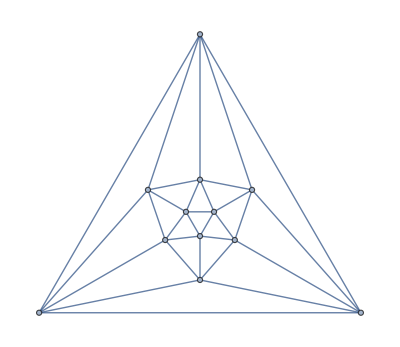

```mathematica
GraphData["IcosahedralGraph"]
```

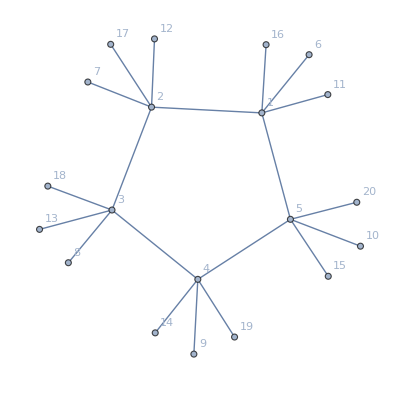

```mathematica
hairy=With[
{n=5},
Graph[EdgeAdd[CycleGraph[n],Flatten[
Table[{
i<->i+n,
i<->i+2*n,
i<->i+3*n
},{i,1,n}]]],GraphLayout->"SpringElectricalEmbedding", VertexLabels->"Name"]
]
```

```mathematica
AbsoluteTiming[
TableForm[
Monitor[
Table[CountSolutions6[hairy,{1<->3,1<->4},{2<->4,2<->5},{3<->5},k,Range[6,20]],{k,Start-1,Start+1024}],k], TableDepth->2
]
]
```

{1042431,{1,1,1,1,1,4,4,4,3,2,4,4,4,4,4},{0,0,0,0,0,0,0}}

{1042432,{1,1,1,1,1,4,4,4,3,3,1,1,1,1,1},{0,0,2,0,0,0,0}}

{1042433,{1,1,1,1,1,4,4,4,3,3,1,1,1,1,2},{0,0,1,0,0,0,0}}

{1042434,{1,1,1,1,1,4,4,4,3,3,1,1,1,1,3},{0,0,2,0,0,0,0}}

{1042435,{1,1,1,1,1,4,4,4,3,3,1,1,1,1,4},{0,0,1,0,0,0,0}}

{1042436,{1,1,1,1,1,4,4,4,3,3,1,1,1,2,1},{0,0,1,0,0,0,0}}

{1042437,{1,1,1,1,1,4,4,4,3,3,1,1,1,2,2},{0,0,0,0,0,0,0}}

{1042438,{1,1,1,1,1,4,4,4,3,3,1,1,1,2,3},{0,0,1,0,0,0,0}}

{1042439,{1,1,1,1,1,4,4,4,3,3,1,1,1,2,4},{0,0,1,0,0,0,0}}

{1042440,{1,1,1,1,1,4,4,4,3,3,1,1,1,3,1},{0,0,2,0,0,0,0}}

{1042441,{1,1,1,1,1,4,4,4,3,3,1,1,1,3,2},{0,0,1,0,0,0,0}}

{1042442,{1,1,1,1,1,4,4,4,3,3,1,1,1,3,3},{0,0,2,0,0,0,0}}

{1042443,{1,1,1,1,1,4,4,4,3,3,1,1,1,3,4},{0,0,1,0,0,0,0}}

{1042444,{1,1,1,1,1,4,4,4,3,3,1,1,1,4,1},{0,0,1,0,0,0,0}}

{1042445,{1,1,1,1,1,4,4,4,3,3,1,1,1,4,2},{0,0,1,0,0,0,0}}

{1042446,{1,1,1,1,1,4,4,4,3,3,1,1,1,4,3},{0,0,1,0,0,0,0}}

{1042447,{1,1,1,1,1,4,4,4,3,3,1,1,1,4,4},{0,0,0,0,0,0,0}}

{1042448,{1,1,1,1,1,4,4,4,3,3,1,1,2,1,1},{0,0,2,0,0,0,0}}

{1042449,{1,1,1,1,1,4,4,4,3,3,1,1,2,1,2},{0,0,1,0,0,0,0}}

{1042450,{1,1,1,1,1,4,4,4,3,3,1,1,2,1,3},{0,0,2,0,0,0,0}}

{1042451,{1,1,1,1,1,4,4,4,3,3,1,1,2,1,4},{0,0,1,0,0,0,0}}

{1042452,{1,1,1,1,1,4,4,4,3,3,1,1,2,2,1},{0,0,1,0,0,0,0}}

{1042453,{1,1,1,1,1,4,4,4,3,3,1,1,2,2,2},{0,0,0,0,0,0,0}}

{1042454,{1,1,1,1,1,4,4,4,3,3,1,1,2,2,3},{0,0,1,0,0,0,0}}

{1042455,{1,1,1,1,1,4,4,4,3,3,1,1,2,2,4},{0,0,1,0,0,0,0}}

{1042456,{1,1,1,1,1,4,4,4,3,3,1,1,2,3,1},{0,0,2,0,0,0,0}}

{1042457,{1,1,1,1,1,4,4,4,3,3,1,1,2,3,2},{0,0,1,0,0,0,0}}

{1042458,{1,1,1,1,1,4,4,4,3,3,1,1,2,3,3},{0,0,2,0,0,0,0}}

{1042459,{1,1,1,1,1,4,4,4,3,3,1,1,2,3,4},{0,0,1,0,0,0,0}}

{1042460,{1,1,1,1,1,4,4,4,3,3,1,1,2,4,1},{0,0,1,0,0,0,0}}

{1042461,{1,1,1,1,1,4,4,4,3,3,1,1,2,4,2},{0,0,1,0,0,0,0}}

{1042462,{1,1,1,1,1,4,4,4,3,3,1,1,2,4,3},{0,0,1,0,0,0,0}}

{1042463,{1,1,1,1,1,4,4,4,3,3,1,1,2,4,4},{0,0,0,0,0,0,0}}

{1042464,{1,1,1,1,1,4,4,4,3,3,1,1,3,1,1},{0,0,0,0,0,0,0}}

{1042465,{1,1,1,1,1,4,4,4,3,3,1,1,3,1,2},{0,0,0,0,0,0,0}}

{1042466,{1,1,1,1,1,4,4,4,3,3,1,1,3,1,3},{0,0,0,0,0,0,0}}

{1042467,{1,1,1,1,1,4,4,4,3,3,1,1,3,1,4},{0,0,0,0,0,0,0}}

{1042468,{1,1,1,1,1,4,4,4,3,3,1,1,3,2,1},{0,0,0,0,0,0,0}}

{1042469,{1,1,1,1,1,4,4,4,3,3,1,1,3,2,2},{0,0,0,0,0,0,0}}

{1042470,{1,1,1,1,1,4,4,4,3,3,1,1,3,2,3},{0,0,0,0,0,0,0}}

{1042471,{1,1,1,1,1,4,4,4,3,3,1,1,3,2,4},{0,0,0,0,0,0,0}}

{1042472,{1,1,1,1,1,4,4,4,3,3,1,1,3,3,1},{0,0,0,0,0,0,0}}

{1042473,{1,1,1,1,1,4,4,4,3,3,1,1,3,3,2},{0,0,0,0,0,0,0}}

{1042474,{1,1,1,1,1,4,4,4,3,3,1,1,3,3,3},{0,0,0,0,0,0,0}}

{1042475,{1,1,1,1,1,4,4,4,3,3,1,1,3,3,4},{0,0,0,0,0,0,0}}

{1042476,{1,1,1,1,1,4,4,4,3,3,1,1,3,4,1},{0,0,0,0,0,0,0}}

{1042477,{1,1,1,1,1,4,4,4,3,3,1,1,3,4,2},{0,0,0,0,0,0,0}}

{1042478,{1,1,1,1,1,4,4,4,3,3,1,1,3,4,3},{0,0,0,0,0,0,0}}

{1042479,{1,1,1,1,1,4,4,4,3,3,1,1,3,4,4},{0,0,0,0,0,0,0}}

{1042480,{1,1,1,1,1,4,4,4,3,3,1,1,4,1,1},{0,0,2,0,0,0,0}}

{1042481,{1,1,1,1,1,4,4,4,3,3,1,1,4,1,2},{0,0,1,0,0,0,0}}

{1042482,{1,1,1,1,1,4,4,4,3,3,1,1,4,1,3},{0,0,2,0,0,0,0}}

{1042483,{1,1,1,1,1,4,4,4,3,3,1,1,4,1,4},{0,0,1,0,0,0,0}}

{1042484,{1,1,1,1,1,4,4,4,3,3,1,1,4,2,1},{0,0,1,0,0,0,0}}

{1042485,{1,1,1,1,1,4,4,4,3,3,1,1,4,2,2},{0,0,0,0,0,0,0}}

{1042486,{1,1,1,1,1,4,4,4,3,3,1,1,4,2,3},{0,0,1,0,0,0,0}}

{1042487,{1,1,1,1,1,4,4,4,3,3,1,1,4,2,4},{0,0,1,0,0,0,0}}

{1042488,{1,1,1,1,1,4,4,4,3,3,1,1,4,3,1},{0,0,2,0,0,0,0}}

{1042489,{1,1,1,1,1,4,4,4,3,3,1,1,4,3,2},{0,0,1,0,0,0,0}}

{1042490,{1,1,1,1,1,4,4,4,3,3,1,1,4,3,3},{0,0,2,0,0,0,0}}

{1042491,{1,1,1,1,1,4,4,4,3,3,1,1,4,3,4},{0,0,1,0,0,0,0}}

{1042492,{1,1,1,1,1,4,4,4,3,3,1,1,4,4,1},{0,0,1,0,0,0,0}}

{1042493,{1,1,1,1,1,4,4,4,3,3,1,1,4,4,2},{0,0,1,0,0,0,0}}

{1042494,{1,1,1,1,1,4,4,4,3,3,1,1,4,4,3},{0,0,1,0,0,0,0}}

{1042495,{1,1,1,1,1,4,4,4,3,3,1,1,4,4,4},{0,0,0,0,0,0,0}}

{1042496,{1,1,1,1,1,4,4,4,3,3,1,2,1,1,1},{0,0,0,0,0,0,0}}

{1042497,{1,1,1,1,1,4,4,4,3,3,1,2,1,1,2},{0,0,0,0,0,0,0}}

{1042498,{1,1,1,1,1,4,4,4,3,3,1,2,1,1,3},{0,0,0,0,0,0,0}}

{1042499,{1,1,1,1,1,4,4,4,3,3,1,2,1,1,4},{0,0,0,0,0,0,0}}

{1042500,{1,1,1,1,1,4,4,4,3,3,1,2,1,2,1},{0,0,0,0,0,0,0}}

{1042501,{1,1,1,1,1,4,4,4,3,3,1,2,1,2,2},{0,0,0,0,0,0,0}}

{1042502,{1,1,1,1,1,4,4,4,3,3,1,2,1,2,3},{0,0,0,0,0,0,0}}

{1042503,{1,1,1,1,1,4,4,4,3,3,1,2,1,2,4},{0,0,0,0,0,0,0}}

{1042504,{1,1,1,1,1,4,4,4,3,3,1,2,1,3,1},{0,0,0,0,0,0,0}}

{1042505,{1,1,1,1,1,4,4,4,3,3,1,2,1,3,2},{0,0,0,0,0,0,0}}

{1042506,{1,1,1,1,1,4,4,4,3,3,1,2,1,3,3},{0,0,0,0,0,0,0}}

{1042507,{1,1,1,1,1,4,4,4,3,3,1,2,1,3,4},{0,0,0,0,0,0,0}}

{1042508,{1,1,1,1,1,4,4,4,3,3,1,2,1,4,1},{0,0,0,0,0,0,0}}

{1042509,{1,1,1,1,1,4,4,4,3,3,1,2,1,4,2},{0,0,0,0,0,0,0}}

{1042510,{1,1,1,1,1,4,4,4,3,3,1,2,1,4,3},{0,0,0,0,0,0,0}}

{1042511,{1,1,1,1,1,4,4,4,3,3,1,2,1,4,4},{0,0,0,0,0,0,0}}

{1042512,{1,1,1,1,1,4,4,4,3,3,1,2,2,1,1},{0,0,0,0,0,0,0}}

{1042513,{1,1,1,1,1,4,4,4,3,3,1,2,2,1,2},{0,0,0,0,0,0,0}}

{1042514,{1,1,1,1,1,4,4,4,3,3,1,2,2,1,3},{0,0,0,0,0,0,0}}

{1042515,{1,1,1,1,1,4,4,4,3,3,1,2,2,1,4},{0,0,0,0,0,0,0}}

{1042516,{1,1,1,1,1,4,4,4,3,3,1,2,2,2,1},{0,0,0,0,0,0,0}}

{1042517,{1,1,1,1,1,4,4,4,3,3,1,2,2,2,2},{0,0,0,0,0,0,0}}

{1042518,{1,1,1,1,1,4,4,4,3,3,1,2,2,2,3},{0,0,0,0,0,0,0}}

{1042519,{1,1,1,1,1,4,4,4,3,3,1,2,2,2,4},{0,0,0,0,0,0,0}}

{1042520,{1,1,1,1,1,4,4,4,3,3,1,2,2,3,1},{0,0,0,0,0,0,0}}

{1042521,{1,1,1,1,1,4,4,4,3,3,1,2,2,3,2},{0,0,0,0,0,0,0}}

{1042522,{1,1,1,1,1,4,4,4,3,3,1,2,2,3,3},{0,0,0,0,0,0,0}}

{1042523,{1,1,1,1,1,4,4,4,3,3,1,2,2,3,4},{0,0,0,0,0,0,0}}

{1042524,{1,1,1,1,1,4,4,4,3,3,1,2,2,4,1},{0,0,0,0,0,0,0}}

{1042525,{1,1,1,1,1,4,4,4,3,3,1,2,2,4,2},{0,0,0,0,0,0,0}}

{1042526,{1,1,1,1,1,4,4,4,3,3,1,2,2,4,3},{0,0,0,0,0,0,0}}

{1042527,{1,1,1,1,1,4,4,4,3,3,1,2,2,4,4},{0,0,0,0,0,0,0}}

{1042528,{1,1,1,1,1,4,4,4,3,3,1,2,3,1,1},{0,0,0,0,0,0,0}}

{1042529,{1,1,1,1,1,4,4,4,3,3,1,2,3,1,2},{0,0,0,0,0,0,0}}

{1042530,{1,1,1,1,1,4,4,4,3,3,1,2,3,1,3},{0,0,0,0,0,0,0}}

{1042531,{1,1,1,1,1,4,4,4,3,3,1,2,3,1,4},{0,0,0,0,0,0,0}}

{1042532,{1,1,1,1,1,4,4,4,3,3,1,2,3,2,1},{0,0,0,0,0,0,0}}

{1042533,{1,1,1,1,1,4,4,4,3,3,1,2,3,2,2},{0,0,0,0,0,0,0}}

{1042534,{1,1,1,1,1,4,4,4,3,3,1,2,3,2,3},{0,0,0,0,0,0,0}}

{1042535,{1,1,1,1,1,4,4,4,3,3,1,2,3,2,4},{0,0,0,0,0,0,0}}

{1042536,{1,1,1,1,1,4,4,4,3,3,1,2,3,3,1},{0,0,0,0,0,0,0}}

{1042537,{1,1,1,1,1,4,4,4,3,3,1,2,3,3,2},{0,0,0,0,0,0,0}}

{1042538,{1,1,1,1,1,4,4,4,3,3,1,2,3,3,3},{0,0,0,0,0,0,0}}

{1042539,{1,1,1,1,1,4,4,4,3,3,1,2,3,3,4},{0,0,0,0,0,0,0}}

{1042540,{1,1,1,1,1,4,4,4,3,3,1,2,3,4,1},{0,0,0,0,0,0,0}}

{1042541,{1,1,1,1,1,4,4,4,3,3,1,2,3,4,2},{0,0,0,0,0,0,0}}

{1042542,{1,1,1,1,1,4,4,4,3,3,1,2,3,4,3},{0,0,0,0,0,0,0}}

{1042543,{1,1,1,1,1,4,4,4,3,3,1,2,3,4,4},{0,0,0,0,0,0,0}}

{1042544,{1,1,1,1,1,4,4,4,3,3,1,2,4,1,1},{0,0,0,0,0,0,0}}

{1042545,{1,1,1,1,1,4,4,4,3,3,1,2,4,1,2},{0,0,0,0,0,0,0}}

{1042546,{1,1,1,1,1,4,4,4,3,3,1,2,4,1,3},{0,0,0,0,0,0,0}}

{1042547,{1,1,1,1,1,4,4,4,3,3,1,2,4,1,4},{0,0,0,0,0,0,0}}

{1042548,{1,1,1,1,1,4,4,4,3,3,1,2,4,2,1},{0,0,0,0,0,0,0}}

{1042549,{1,1,1,1,1,4,4,4,3,3,1,2,4,2,2},{0,0,0,0,0,0,0}}

{1042550,{1,1,1,1,1,4,4,4,3,3,1,2,4,2,3},{0,0,0,0,0,0,0}}

{1042551,{1,1,1,1,1,4,4,4,3,3,1,2,4,2,4},{0,0,0,0,0,0,0}}

{1042552,{1,1,1,1,1,4,4,4,3,3,1,2,4,3,1},{0,0,0,0,0,0,0}}

{1042553,{1,1,1,1,1,4,4,4,3,3,1,2,4,3,2},{0,0,0,0,0,0,0}}

{1042554,{1,1,1,1,1,4,4,4,3,3,1,2,4,3,3},{0,0,0,0,0,0,0}}

{1042555,{1,1,1,1,1,4,4,4,3,3,1,2,4,3,4},{0,0,0,0,0,0,0}}

{1042556,{1,1,1,1,1,4,4,4,3,3,1,2,4,4,1},{0,0,0,0,0,0,0}}

{1042557,{1,1,1,1,1,4,4,4,3,3,1,2,4,4,2},{0,0,0,0,0,0,0}}

{1042558,{1,1,1,1,1,4,4,4,3,3,1,2,4,4,3},{0,0,0,0,0,0,0}}

{1042559,{1,1,1,1,1,4,4,4,3,3,1,2,4,4,4},{0,0,0,0,0,0,0}}

{1042560,{1,1,1,1,1,4,4,4,3,3,1,3,1,1,1},{0,0,2,0,0,0,0}}

{1042561,{1,1,1,1,1,4,4,4,3,3,1,3,1,1,2},{0,0,1,0,0,0,0}}

{1042562,{1,1,1,1,1,4,4,4,3,3,1,3,1,1,3},{0,0,2,0,0,0,0}}

{1042563,{1,1,1,1,1,4,4,4,3,3,1,3,1,1,4},{0,0,1,0,0,0,0}}

{1042564,{1,1,1,1,1,4,4,4,3,3,1,3,1,2,1},{0,0,1,0,0,0,0}}

{1042565,{1,1,1,1,1,4,4,4,3,3,1,3,1,2,2},{0,0,0,0,0,0,0}}

{1042566,{1,1,1,1,1,4,4,4,3,3,1,3,1,2,3},{0,0,1,0,0,0,0}}

{1042567,{1,1,1,1,1,4,4,4,3,3,1,3,1,2,4},{0,0,1,0,0,0,0}}

{1042568,{1,1,1,1,1,4,4,4,3,3,1,3,1,3,1},{0,0,2,0,0,0,0}}

{1042569,{1,1,1,1,1,4,4,4,3,3,1,3,1,3,2},{0,0,1,0,0,0,0}}

{1042570,{1,1,1,1,1,4,4,4,3,3,1,3,1,3,3},{0,0,2,0,0,0,0}}

{1042571,{1,1,1,1,1,4,4,4,3,3,1,3,1,3,4},{0,0,1,0,0,0,0}}

{1042572,{1,1,1,1,1,4,4,4,3,3,1,3,1,4,1},{0,0,1,0,0,0,0}}

{1042573,{1,1,1,1,1,4,4,4,3,3,1,3,1,4,2},{0,0,1,0,0,0,0}}

{1042574,{1,1,1,1,1,4,4,4,3,3,1,3,1,4,3},{0,0,1,0,0,0,0}}

{1042575,{1,1,1,1,1,4,4,4,3,3,1,3,1,4,4},{0,0,0,0,0,0,0}}

{1042576,{1,1,1,1,1,4,4,4,3,3,1,3,2,1,1},{0,0,2,0,0,0,0}}

{1042577,{1,1,1,1,1,4,4,4,3,3,1,3,2,1,2},{0,0,1,0,0,0,0}}

{1042578,{1,1,1,1,1,4,4,4,3,3,1,3,2,1,3},{0,0,2,0,0,0,0}}

{1042579,{1,1,1,1,1,4,4,4,3,3,1,3,2,1,4},{0,0,1,0,0,0,0}}

{1042580,{1,1,1,1,1,4,4,4,3,3,1,3,2,2,1},{0,0,1,0,0,0,0}}

{1042581,{1,1,1,1,1,4,4,4,3,3,1,3,2,2,2},{0,0,0,0,0,0,0}}

{1042582,{1,1,1,1,1,4,4,4,3,3,1,3,2,2,3},{0,0,1,0,0,0,0}}

{1042583,{1,1,1,1,1,4,4,4,3,3,1,3,2,2,4},{0,0,1,0,0,0,0}}

{1042584,{1,1,1,1,1,4,4,4,3,3,1,3,2,3,1},{0,0,2,0,0,0,0}}

{1042585,{1,1,1,1,1,4,4,4,3,3,1,3,2,3,2},{0,0,1,0,0,0,0}}

{1042586,{1,1,1,1,1,4,4,4,3,3,1,3,2,3,3},{0,0,2,0,0,0,0}}

{1042587,{1,1,1,1,1,4,4,4,3,3,1,3,2,3,4},{0,0,1,0,0,0,0}}

{1042588,{1,1,1,1,1,4,4,4,3,3,1,3,2,4,1},{0,0,1,0,0,0,0}}

{1042589,{1,1,1,1,1,4,4,4,3,3,1,3,2,4,2},{0,0,1,0,0,0,0}}

{1042590,{1,1,1,1,1,4,4,4,3,3,1,3,2,4,3},{0,0,1,0,0,0,0}}

{1042591,{1,1,1,1,1,4,4,4,3,3,1,3,2,4,4},{0,0,0,0,0,0,0}}

{1042592,{1,1,1,1,1,4,4,4,3,3,1,3,3,1,1},{0,0,0,0,0,0,0}}

{1042593,{1,1,1,1,1,4,4,4,3,3,1,3,3,1,2},{0,0,0,0,0,0,0}}

{1042594,{1,1,1,1,1,4,4,4,3,3,1,3,3,1,3},{0,0,0,0,0,0,0}}

{1042595,{1,1,1,1,1,4,4,4,3,3,1,3,3,1,4},{0,0,0,0,0,0,0}}

{1042596,{1,1,1,1,1,4,4,4,3,3,1,3,3,2,1},{0,0,0,0,0,0,0}}

{1042597,{1,1,1,1,1,4,4,4,3,3,1,3,3,2,2},{0,0,0,0,0,0,0}}

{1042598,{1,1,1,1,1,4,4,4,3,3,1,3,3,2,3},{0,0,0,0,0,0,0}}

{1042599,{1,1,1,1,1,4,4,4,3,3,1,3,3,2,4},{0,0,0,0,0,0,0}}

{1042600,{1,1,1,1,1,4,4,4,3,3,1,3,3,3,1},{0,0,0,0,0,0,0}}

{1042601,{1,1,1,1,1,4,4,4,3,3,1,3,3,3,2},{0,0,0,0,0,0,0}}

{1042602,{1,1,1,1,1,4,4,4,3,3,1,3,3,3,3},{0,0,0,0,0,0,0}}

{1042603,{1,1,1,1,1,4,4,4,3,3,1,3,3,3,4},{0,0,0,0,0,0,0}}

{1042604,{1,1,1,1,1,4,4,4,3,3,1,3,3,4,1},{0,0,0,0,0,0,0}}

{1042605,{1,1,1,1,1,4,4,4,3,3,1,3,3,4,2},{0,0,0,0,0,0,0}}

{1042606,{1,1,1,1,1,4,4,4,3,3,1,3,3,4,3},{0,0,0,0,0,0,0}}

{1042607,{1,1,1,1,1,4,4,4,3,3,1,3,3,4,4},{0,0,0,0,0,0,0}}

{1042608,{1,1,1,1,1,4,4,4,3,3,1,3,4,1,1},{0,0,2,0,0,0,0}}

{1042609,{1,1,1,1,1,4,4,4,3,3,1,3,4,1,2},{0,0,1,0,0,0,0}}

{1042610,{1,1,1,1,1,4,4,4,3,3,1,3,4,1,3},{0,0,2,0,0,0,0}}

{1042611,{1,1,1,1,1,4,4,4,3,3,1,3,4,1,4},{0,0,1,0,0,0,0}}

{1042612,{1,1,1,1,1,4,4,4,3,3,1,3,4,2,1},{0,0,1,0,0,0,0}}

{1042613,{1,1,1,1,1,4,4,4,3,3,1,3,4,2,2},{0,0,0,0,0,0,0}}

{1042614,{1,1,1,1,1,4,4,4,3,3,1,3,4,2,3},{0,0,1,0,0,0,0}}

{1042615,{1,1,1,1,1,4,4,4,3,3,1,3,4,2,4},{0,0,1,0,0,0,0}}

{1042616,{1,1,1,1,1,4,4,4,3,3,1,3,4,3,1},{0,0,2,0,0,0,0}}

{1042617,{1,1,1,1,1,4,4,4,3,3,1,3,4,3,2},{0,0,1,0,0,0,0}}

{1042618,{1,1,1,1,1,4,4,4,3,3,1,3,4,3,3},{0,0,2,0,0,0,0}}

{1042619,{1,1,1,1,1,4,4,4,3,3,1,3,4,3,4},{0,0,1,0,0,0,0}}

{1042620,{1,1,1,1,1,4,4,4,3,3,1,3,4,4,1},{0,0,1,0,0,0,0}}

{1042621,{1,1,1,1,1,4,4,4,3,3,1,3,4,4,2},{0,0,1,0,0,0,0}}

{1042622,{1,1,1,1,1,4,4,4,3,3,1,3,4,4,3},{0,0,1,0,0,0,0}}

{1042623,{1,1,1,1,1,4,4,4,3,3,1,3,4,4,4},{0,0,0,0,0,0,0}}

{1042624,{1,1,1,1,1,4,4,4,3,3,1,4,1,1,1},{0,0,2,0,0,0,0}}

{1042625,{1,1,1,1,1,4,4,4,3,3,1,4,1,1,2},{0,0,1,0,0,0,0}}

{1042626,{1,1,1,1,1,4,4,4,3,3,1,4,1,1,3},{0,0,2,0,0,0,0}}

{1042627,{1,1,1,1,1,4,4,4,3,3,1,4,1,1,4},{0,0,1,0,0,0,0}}

{1042628,{1,1,1,1,1,4,4,4,3,3,1,4,1,2,1},{0,0,1,0,0,0,0}}

{1042629,{1,1,1,1,1,4,4,4,3,3,1,4,1,2,2},{0,0,0,0,0,0,0}}

{1042630,{1,1,1,1,1,4,4,4,3,3,1,4,1,2,3},{0,0,1,0,0,0,0}}

{1042631,{1,1,1,1,1,4,4,4,3,3,1,4,1,2,4},{0,0,1,0,0,0,0}}

{1042632,{1,1,1,1,1,4,4,4,3,3,1,4,1,3,1},{0,0,2,0,0,0,0}}

{1042633,{1,1,1,1,1,4,4,4,3,3,1,4,1,3,2},{0,0,1,0,0,0,0}}

{1042634,{1,1,1,1,1,4,4,4,3,3,1,4,1,3,3},{0,0,2,0,0,0,0}}

{1042635,{1,1,1,1,1,4,4,4,3,3,1,4,1,3,4},{0,0,1,0,0,0,0}}

{1042636,{1,1,1,1,1,4,4,4,3,3,1,4,1,4,1},{0,0,1,0,0,0,0}}

{1042637,{1,1,1,1,1,4,4,4,3,3,1,4,1,4,2},{0,0,1,0,0,0,0}}

{1042638,{1,1,1,1,1,4,4,4,3,3,1,4,1,4,3},{0,0,1,0,0,0,0}}

{1042639,{1,1,1,1,1,4,4,4,3,3,1,4,1,4,4},{0,0,0,0,0,0,0}}

{1042640,{1,1,1,1,1,4,4,4,3,3,1,4,2,1,1},{0,0,2,0,0,0,0}}

{1042641,{1,1,1,1,1,4,4,4,3,3,1,4,2,1,2},{0,0,1,0,0,0,0}}

{1042642,{1,1,1,1,1,4,4,4,3,3,1,4,2,1,3},{0,0,2,0,0,0,0}}

{1042643,{1,1,1,1,1,4,4,4,3,3,1,4,2,1,4},{0,0,1,0,0,0,0}}

{1042644,{1,1,1,1,1,4,4,4,3,3,1,4,2,2,1},{0,0,1,0,0,0,0}}

{1042645,{1,1,1,1,1,4,4,4,3,3,1,4,2,2,2},{0,0,0,0,0,0,0}}

{1042646,{1,1,1,1,1,4,4,4,3,3,1,4,2,2,3},{0,0,1,0,0,0,0}}

{1042647,{1,1,1,1,1,4,4,4,3,3,1,4,2,2,4},{0,0,1,0,0,0,0}}

{1042648,{1,1,1,1,1,4,4,4,3,3,1,4,2,3,1},{0,0,2,0,0,0,0}}

{1042649,{1,1,1,1,1,4,4,4,3,3,1,4,2,3,2},{0,0,1,0,0,0,0}}

{1042650,{1,1,1,1,1,4,4,4,3,3,1,4,2,3,3},{0,0,2,0,0,0,0}}

{1042651,{1,1,1,1,1,4,4,4,3,3,1,4,2,3,4},{0,0,1,0,0,0,0}}

{1042652,{1,1,1,1,1,4,4,4,3,3,1,4,2,4,1},{0,0,1,0,0,0,0}}

{1042653,{1,1,1,1,1,4,4,4,3,3,1,4,2,4,2},{0,0,1,0,0,0,0}}

{1042654,{1,1,1,1,1,4,4,4,3,3,1,4,2,4,3},{0,0,1,0,0,0,0}}

{1042655,{1,1,1,1,1,4,4,4,3,3,1,4,2,4,4},{0,0,0,0,0,0,0}}

{1042656,{1,1,1,1,1,4,4,4,3,3,1,4,3,1,1},{0,0,0,0,0,0,0}}

{1042657,{1,1,1,1,1,4,4,4,3,3,1,4,3,1,2},{0,0,0,0,0,0,0}}

{1042658,{1,1,1,1,1,4,4,4,3,3,1,4,3,1,3},{0,0,0,0,0,0,0}}

{1042659,{1,1,1,1,1,4,4,4,3,3,1,4,3,1,4},{0,0,0,0,0,0,0}}

{1042660,{1,1,1,1,1,4,4,4,3,3,1,4,3,2,1},{0,0,0,0,0,0,0}}

{1042661,{1,1,1,1,1,4,4,4,3,3,1,4,3,2,2},{0,0,0,0,0,0,0}}

{1042662,{1,1,1,1,1,4,4,4,3,3,1,4,3,2,3},{0,0,0,0,0,0,0}}

{1042663,{1,1,1,1,1,4,4,4,3,3,1,4,3,2,4},{0,0,0,0,0,0,0}}

{1042664,{1,1,1,1,1,4,4,4,3,3,1,4,3,3,1},{0,0,0,0,0,0,0}}

{1042665,{1,1,1,1,1,4,4,4,3,3,1,4,3,3,2},{0,0,0,0,0,0,0}}

{1042666,{1,1,1,1,1,4,4,4,3,3,1,4,3,3,3},{0,0,0,0,0,0,0}}

{1042667,{1,1,1,1,1,4,4,4,3,3,1,4,3,3,4},{0,0,0,0,0,0,0}}

{1042668,{1,1,1,1,1,4,4,4,3,3,1,4,3,4,1},{0,0,0,0,0,0,0}}

{1042669,{1,1,1,1,1,4,4,4,3,3,1,4,3,4,2},{0,0,0,0,0,0,0}}

{1042670,{1,1,1,1,1,4,4,4,3,3,1,4,3,4,3},{0,0,0,0,0,0,0}}

{1042671,{1,1,1,1,1,4,4,4,3,3,1,4,3,4,4},{0,0,0,0,0,0,0}}

{1042672,{1,1,1,1,1,4,4,4,3,3,1,4,4,1,1},{0,0,2,0,0,0,0}}

{1042673,{1,1,1,1,1,4,4,4,3,3,1,4,4,1,2},{0,0,1,0,0,0,0}}

{1042674,{1,1,1,1,1,4,4,4,3,3,1,4,4,1,3},{0,0,2,0,0,0,0}}

{1042675,{1,1,1,1,1,4,4,4,3,3,1,4,4,1,4},{0,0,1,0,0,0,0}}

{1042676,{1,1,1,1,1,4,4,4,3,3,1,4,4,2,1},{0,0,1,0,0,0,0}}

{1042677,{1,1,1,1,1,4,4,4,3,3,1,4,4,2,2},{0,0,0,0,0,0,0}}

{1042678,{1,1,1,1,1,4,4,4,3,3,1,4,4,2,3},{0,0,1,0,0,0,0}}

{1042679,{1,1,1,1,1,4,4,4,3,3,1,4,4,2,4},{0,0,1,0,0,0,0}}

{1042680,{1,1,1,1,1,4,4,4,3,3,1,4,4,3,1},{0,0,2,0,0,0,0}}

{1042681,{1,1,1,1,1,4,4,4,3,3,1,4,4,3,2},{0,0,1,0,0,0,0}}

{1042682,{1,1,1,1,1,4,4,4,3,3,1,4,4,3,3},{0,0,2,0,0,0,0}}

{1042683,{1,1,1,1,1,4,4,4,3,3,1,4,4,3,4},{0,0,1,0,0,0,0}}

{1042684,{1,1,1,1,1,4,4,4,3,3,1,4,4,4,1},{0,0,1,0,0,0,0}}

{1042685,{1,1,1,1,1,4,4,4,3,3,1,4,4,4,2},{0,0,1,0,0,0,0}}

{1042686,{1,1,1,1,1,4,4,4,3,3,1,4,4,4,3},{0,0,1,0,0,0,0}}

{1042687,{1,1,1,1,1,4,4,4,3,3,1,4,4,4,4},{0,0,0,0,0,0,0}}

{1042688,{1,1,1,1,1,4,4,4,3,3,2,1,1,1,1},{0,0,2,0,0,0,0}}

{1042689,{1,1,1,1,1,4,4,4,3,3,2,1,1,1,2},{0,0,1,0,0,0,0}}

{1042690,{1,1,1,1,1,4,4,4,3,3,2,1,1,1,3},{0,0,2,0,0,0,0}}

{1042691,{1,1,1,1,1,4,4,4,3,3,2,1,1,1,4},{0,0,1,0,0,0,0}}

{1042692,{1,1,1,1,1,4,4,4,3,3,2,1,1,2,1},{0,0,1,0,0,0,0}}

{1042693,{1,1,1,1,1,4,4,4,3,3,2,1,1,2,2},{0,0,0,0,0,0,0}}

{1042694,{1,1,1,1,1,4,4,4,3,3,2,1,1,2,3},{0,0,1,0,0,0,0}}

{1042695,{1,1,1,1,1,4,4,4,3,3,2,1,1,2,4},{0,0,1,0,0,0,0}}

{1042696,{1,1,1,1,1,4,4,4,3,3,2,1,1,3,1},{0,0,2,0,0,0,0}}

{1042697,{1,1,1,1,1,4,4,4,3,3,2,1,1,3,2},{0,0,1,0,0,0,0}}

{1042698,{1,1,1,1,1,4,4,4,3,3,2,1,1,3,3},{0,0,2,0,0,0,0}}

{1042699,{1,1,1,1,1,4,4,4,3,3,2,1,1,3,4},{0,0,1,0,0,0,0}}

{1042700,{1,1,1,1,1,4,4,4,3,3,2,1,1,4,1},{0,0,1,0,0,0,0}}

{1042701,{1,1,1,1,1,4,4,4,3,3,2,1,1,4,2},{0,0,1,0,0,0,0}}

{1042702,{1,1,1,1,1,4,4,4,3,3,2,1,1,4,3},{0,0,1,0,0,0,0}}

{1042703,{1,1,1,1,1,4,4,4,3,3,2,1,1,4,4},{0,0,0,0,0,0,0}}

{1042704,{1,1,1,1,1,4,4,4,3,3,2,1,2,1,1},{0,0,2,0,0,0,0}}

{1042705,{1,1,1,1,1,4,4,4,3,3,2,1,2,1,2},{0,0,1,0,0,0,0}}

{1042706,{1,1,1,1,1,4,4,4,3,3,2,1,2,1,3},{0,0,2,0,0,0,0}}

{1042707,{1,1,1,1,1,4,4,4,3,3,2,1,2,1,4},{0,0,1,0,0,0,0}}

{1042708,{1,1,1,1,1,4,4,4,3,3,2,1,2,2,1},{0,0,1,0,0,0,0}}

{1042709,{1,1,1,1,1,4,4,4,3,3,2,1,2,2,2},{0,0,0,0,0,0,0}}

{1042710,{1,1,1,1,1,4,4,4,3,3,2,1,2,2,3},{0,0,1,0,0,0,0}}

{1042711,{1,1,1,1,1,4,4,4,3,3,2,1,2,2,4},{0,0,1,0,0,0,0}}

{1042712,{1,1,1,1,1,4,4,4,3,3,2,1,2,3,1},{0,0,2,0,0,0,0}}

{1042713,{1,1,1,1,1,4,4,4,3,3,2,1,2,3,2},{0,0,1,0,0,0,0}}

{1042714,{1,1,1,1,1,4,4,4,3,3,2,1,2,3,3},{0,0,2,0,0,0,0}}

{1042715,{1,1,1,1,1,4,4,4,3,3,2,1,2,3,4},{0,0,1,0,0,0,0}}

{1042716,{1,1,1,1,1,4,4,4,3,3,2,1,2,4,1},{0,0,1,0,0,0,0}}

{1042717,{1,1,1,1,1,4,4,4,3,3,2,1,2,4,2},{0,0,1,0,0,0,0}}

{1042718,{1,1,1,1,1,4,4,4,3,3,2,1,2,4,3},{0,0,1,0,0,0,0}}

{1042719,{1,1,1,1,1,4,4,4,3,3,2,1,2,4,4},{0,0,0,0,0,0,0}}

{1042720,{1,1,1,1,1,4,4,4,3,3,2,1,3,1,1},{0,0,0,0,0,0,0}}

{1042721,{1,1,1,1,1,4,4,4,3,3,2,1,3,1,2},{0,0,0,0,0,0,0}}

{1042722,{1,1,1,1,1,4,4,4,3,3,2,1,3,1,3},{0,0,0,0,0,0,0}}

{1042723,{1,1,1,1,1,4,4,4,3,3,2,1,3,1,4},{0,0,0,0,0,0,0}}

{1042724,{1,1,1,1,1,4,4,4,3,3,2,1,3,2,1},{0,0,0,0,0,0,0}}

{1042725,{1,1,1,1,1,4,4,4,3,3,2,1,3,2,2},{0,0,0,0,0,0,0}}

{1042726,{1,1,1,1,1,4,4,4,3,3,2,1,3,2,3},{0,0,0,0,0,0,0}}

{1042727,{1,1,1,1,1,4,4,4,3,3,2,1,3,2,4},{0,0,0,0,0,0,0}}

{1042728,{1,1,1,1,1,4,4,4,3,3,2,1,3,3,1},{0,0,0,0,0,0,0}}

{1042729,{1,1,1,1,1,4,4,4,3,3,2,1,3,3,2},{0,0,0,0,0,0,0}}

{1042730,{1,1,1,1,1,4,4,4,3,3,2,1,3,3,3},{0,0,0,0,0,0,0}}

{1042731,{1,1,1,1,1,4,4,4,3,3,2,1,3,3,4},{0,0,0,0,0,0,0}}

{1042732,{1,1,1,1,1,4,4,4,3,3,2,1,3,4,1},{0,0,0,0,0,0,0}}

{1042733,{1,1,1,1,1,4,4,4,3,3,2,1,3,4,2},{0,0,0,0,0,0,0}}

{1042734,{1,1,1,1,1,4,4,4,3,3,2,1,3,4,3},{0,0,0,0,0,0,0}}

{1042735,{1,1,1,1,1,4,4,4,3,3,2,1,3,4,4},{0,0,0,0,0,0,0}}

{1042736,{1,1,1,1,1,4,4,4,3,3,2,1,4,1,1},{0,0,2,0,0,0,0}}

{1042737,{1,1,1,1,1,4,4,4,3,3,2,1,4,1,2},{0,0,1,0,0,0,0}}

{1042738,{1,1,1,1,1,4,4,4,3,3,2,1,4,1,3},{0,0,2,0,0,0,0}}

{1042739,{1,1,1,1,1,4,4,4,3,3,2,1,4,1,4},{0,0,1,0,0,0,0}}

{1042740,{1,1,1,1,1,4,4,4,3,3,2,1,4,2,1},{0,0,1,0,0,0,0}}

{1042741,{1,1,1,1,1,4,4,4,3,3,2,1,4,2,2},{0,0,0,0,0,0,0}}

{1042742,{1,1,1,1,1,4,4,4,3,3,2,1,4,2,3},{0,0,1,0,0,0,0}}

{1042743,{1,1,1,1,1,4,4,4,3,3,2,1,4,2,4},{0,0,1,0,0,0,0}}

{1042744,{1,1,1,1,1,4,4,4,3,3,2,1,4,3,1},{0,0,2,0,0,0,0}}

{1042745,{1,1,1,1,1,4,4,4,3,3,2,1,4,3,2},{0,0,1,0,0,0,0}}

{1042746,{1,1,1,1,1,4,4,4,3,3,2,1,4,3,3},{0,0,2,0,0,0,0}}

{1042747,{1,1,1,1,1,4,4,4,3,3,2,1,4,3,4},{0,0,1,0,0,0,0}}

{1042748,{1,1,1,1,1,4,4,4,3,3,2,1,4,4,1},{0,0,1,0,0,0,0}}

{1042749,{1,1,1,1,1,4,4,4,3,3,2,1,4,4,2},{0,0,1,0,0,0,0}}

{1042750,{1,1,1,1,1,4,4,4,3,3,2,1,4,4,3},{0,0,1,0,0,0,0}}

{1042751,{1,1,1,1,1,4,4,4,3,3,2,1,4,4,4},{0,0,0,0,0,0,0}}

{1042752,{1,1,1,1,1,4,4,4,3,3,2,2,1,1,1},{0,0,0,0,0,0,0}}

{1042753,{1,1,1,1,1,4,4,4,3,3,2,2,1,1,2},{0,0,0,0,0,0,0}}

{1042754,{1,1,1,1,1,4,4,4,3,3,2,2,1,1,3},{0,0,0,0,0,0,0}}

{1042755,{1,1,1,1,1,4,4,4,3,3,2,2,1,1,4},{0,0,0,0,0,0,0}}

{1042756,{1,1,1,1,1,4,4,4,3,3,2,2,1,2,1},{0,0,0,0,0,0,0}}

{1042757,{1,1,1,1,1,4,4,4,3,3,2,2,1,2,2},{0,0,0,0,0,0,0}}

{1042758,{1,1,1,1,1,4,4,4,3,3,2,2,1,2,3},{0,0,0,0,0,0,0}}

{1042759,{1,1,1,1,1,4,4,4,3,3,2,2,1,2,4},{0,0,0,0,0,0,0}}

{1042760,{1,1,1,1,1,4,4,4,3,3,2,2,1,3,1},{0,0,0,0,0,0,0}}

{1042761,{1,1,1,1,1,4,4,4,3,3,2,2,1,3,2},{0,0,0,0,0,0,0}}

{1042762,{1,1,1,1,1,4,4,4,3,3,2,2,1,3,3},{0,0,0,0,0,0,0}}

{1042763,{1,1,1,1,1,4,4,4,3,3,2,2,1,3,4},{0,0,0,0,0,0,0}}

{1042764,{1,1,1,1,1,4,4,4,3,3,2,2,1,4,1},{0,0,0,0,0,0,0}}

{1042765,{1,1,1,1,1,4,4,4,3,3,2,2,1,4,2},{0,0,0,0,0,0,0}}

{1042766,{1,1,1,1,1,4,4,4,3,3,2,2,1,4,3},{0,0,0,0,0,0,0}}

{1042767,{1,1,1,1,1,4,4,4,3,3,2,2,1,4,4},{0,0,0,0,0,0,0}}

{1042768,{1,1,1,1,1,4,4,4,3,3,2,2,2,1,1},{0,0,0,0,0,0,0}}

{1042769,{1,1,1,1,1,4,4,4,3,3,2,2,2,1,2},{0,0,0,0,0,0,0}}

{1042770,{1,1,1,1,1,4,4,4,3,3,2,2,2,1,3},{0,0,0,0,0,0,0}}

{1042771,{1,1,1,1,1,4,4,4,3,3,2,2,2,1,4},{0,0,0,0,0,0,0}}

{1042772,{1,1,1,1,1,4,4,4,3,3,2,2,2,2,1},{0,0,0,0,0,0,0}}

{1042773,{1,1,1,1,1,4,4,4,3,3,2,2,2,2,2},{0,0,0,0,0,0,0}}

{1042774,{1,1,1,1,1,4,4,4,3,3,2,2,2,2,3},{0,0,0,0,0,0,0}}

{1042775,{1,1,1,1,1,4,4,4,3,3,2,2,2,2,4},{0,0,0,0,0,0,0}}

{1042776,{1,1,1,1,1,4,4,4,3,3,2,2,2,3,1},{0,0,0,0,0,0,0}}

{1042777,{1,1,1,1,1,4,4,4,3,3,2,2,2,3,2},{0,0,0,0,0,0,0}}

{1042778,{1,1,1,1,1,4,4,4,3,3,2,2,2,3,3},{0,0,0,0,0,0,0}}

{1042779,{1,1,1,1,1,4,4,4,3,3,2,2,2,3,4},{0,0,0,0,0,0,0}}

{1042780,{1,1,1,1,1,4,4,4,3,3,2,2,2,4,1},{0,0,0,0,0,0,0}}

{1042781,{1,1,1,1,1,4,4,4,3,3,2,2,2,4,2},{0,0,0,0,0,0,0}}

{1042782,{1,1,1,1,1,4,4,4,3,3,2,2,2,4,3},{0,0,0,0,0,0,0}}

{1042783,{1,1,1,1,1,4,4,4,3,3,2,2,2,4,4},{0,0,0,0,0,0,0}}

{1042784,{1,1,1,1,1,4,4,4,3,3,2,2,3,1,1},{0,0,0,0,0,0,0}}

{1042785,{1,1,1,1,1,4,4,4,3,3,2,2,3,1,2},{0,0,0,0,0,0,0}}

{1042786,{1,1,1,1,1,4,4,4,3,3,2,2,3,1,3},{0,0,0,0,0,0,0}}

{1042787,{1,1,1,1,1,4,4,4,3,3,2,2,3,1,4},{0,0,0,0,0,0,0}}

{1042788,{1,1,1,1,1,4,4,4,3,3,2,2,3,2,1},{0,0,0,0,0,0,0}}

{1042789,{1,1,1,1,1,4,4,4,3,3,2,2,3,2,2},{0,0,0,0,0,0,0}}

{1042790,{1,1,1,1,1,4,4,4,3,3,2,2,3,2,3},{0,0,0,0,0,0,0}}

{1042791,{1,1,1,1,1,4,4,4,3,3,2,2,3,2,4},{0,0,0,0,0,0,0}}

{1042792,{1,1,1,1,1,4,4,4,3,3,2,2,3,3,1},{0,0,0,0,0,0,0}}

{1042793,{1,1,1,1,1,4,4,4,3,3,2,2,3,3,2},{0,0,0,0,0,0,0}}

{1042794,{1,1,1,1,1,4,4,4,3,3,2,2,3,3,3},{0,0,0,0,0,0,0}}

{1042795,{1,1,1,1,1,4,4,4,3,3,2,2,3,3,4},{0,0,0,0,0,0,0}}

{1042796,{1,1,1,1,1,4,4,4,3,3,2,2,3,4,1},{0,0,0,0,0,0,0}}

{1042797,{1,1,1,1,1,4,4,4,3,3,2,2,3,4,2},{0,0,0,0,0,0,0}}

{1042798,{1,1,1,1,1,4,4,4,3,3,2,2,3,4,3},{0,0,0,0,0,0,0}}

{1042799,{1,1,1,1,1,4,4,4,3,3,2,2,3,4,4},{0,0,0,0,0,0,0}}

{1042800,{1,1,1,1,1,4,4,4,3,3,2,2,4,1,1},{0,0,0,0,0,0,0}}

{1042801,{1,1,1,1,1,4,4,4,3,3,2,2,4,1,2},{0,0,0,0,0,0,0}}

{1042802,{1,1,1,1,1,4,4,4,3,3,2,2,4,1,3},{0,0,0,0,0,0,0}}

{1042803,{1,1,1,1,1,4,4,4,3,3,2,2,4,1,4},{0,0,0,0,0,0,0}}

{1042804,{1,1,1,1,1,4,4,4,3,3,2,2,4,2,1},{0,0,0,0,0,0,0}}

{1042805,{1,1,1,1,1,4,4,4,3,3,2,2,4,2,2},{0,0,0,0,0,0,0}}

{1042806,{1,1,1,1,1,4,4,4,3,3,2,2,4,2,3},{0,0,0,0,0,0,0}}

{1042807,{1,1,1,1,1,4,4,4,3,3,2,2,4,2,4},{0,0,0,0,0,0,0}}

{1042808,{1,1,1,1,1,4,4,4,3,3,2,2,4,3,1},{0,0,0,0,0,0,0}}

{1042809,{1,1,1,1,1,4,4,4,3,3,2,2,4,3,2},{0,0,0,0,0,0,0}}

{1042810,{1,1,1,1,1,4,4,4,3,3,2,2,4,3,3},{0,0,0,0,0,0,0}}

{1042811,{1,1,1,1,1,4,4,4,3,3,2,2,4,3,4},{0,0,0,0,0,0,0}}

{1042812,{1,1,1,1,1,4,4,4,3,3,2,2,4,4,1},{0,0,0,0,0,0,0}}

{1042813,{1,1,1,1,1,4,4,4,3,3,2,2,4,4,2},{0,0,0,0,0,0,0}}

{1042814,{1,1,1,1,1,4,4,4,3,3,2,2,4,4,3},{0,0,0,0,0,0,0}}

{1042815,{1,1,1,1,1,4,4,4,3,3,2,2,4,4,4},{0,0,0,0,0,0,0}}

{1042816,{1,1,1,1,1,4,4,4,3,3,2,3,1,1,1},{0,0,2,0,0,0,0}}

{1042817,{1,1,1,1,1,4,4,4,3,3,2,3,1,1,2},{0,0,1,0,0,0,0}}

{1042818,{1,1,1,1,1,4,4,4,3,3,2,3,1,1,3},{0,0,2,0,0,0,0}}

{1042819,{1,1,1,1,1,4,4,4,3,3,2,3,1,1,4},{0,0,1,0,0,0,0}}

{1042820,{1,1,1,1,1,4,4,4,3,3,2,3,1,2,1},{0,0,1,0,0,0,0}}

{1042821,{1,1,1,1,1,4,4,4,3,3,2,3,1,2,2},{0,0,0,0,0,0,0}}

{1042822,{1,1,1,1,1,4,4,4,3,3,2,3,1,2,3},{0,0,1,0,0,0,0}}

{1042823,{1,1,1,1,1,4,4,4,3,3,2,3,1,2,4},{0,0,1,0,0,0,0}}

{1042824,{1,1,1,1,1,4,4,4,3,3,2,3,1,3,1},{0,0,2,0,0,0,0}}

{1042825,{1,1,1,1,1,4,4,4,3,3,2,3,1,3,2},{0,0,1,0,0,0,0}}

{1042826,{1,1,1,1,1,4,4,4,3,3,2,3,1,3,3},{0,0,2,0,0,0,0}}

{1042827,{1,1,1,1,1,4,4,4,3,3,2,3,1,3,4},{0,0,1,0,0,0,0}}

{1042828,{1,1,1,1,1,4,4,4,3,3,2,3,1,4,1},{0,0,1,0,0,0,0}}

{1042829,{1,1,1,1,1,4,4,4,3,3,2,3,1,4,2},{0,0,1,0,0,0,0}}

{1042830,{1,1,1,1,1,4,4,4,3,3,2,3,1,4,3},{0,0,1,0,0,0,0}}

{1042831,{1,1,1,1,1,4,4,4,3,3,2,3,1,4,4},{0,0,0,0,0,0,0}}

{1042832,{1,1,1,1,1,4,4,4,3,3,2,3,2,1,1},{0,0,2,0,0,0,0}}

{1042833,{1,1,1,1,1,4,4,4,3,3,2,3,2,1,2},{0,0,1,0,0,0,0}}

{1042834,{1,1,1,1,1,4,4,4,3,3,2,3,2,1,3},{0,0,2,0,0,0,0}}

{1042835,{1,1,1,1,1,4,4,4,3,3,2,3,2,1,4},{0,0,1,0,0,0,0}}

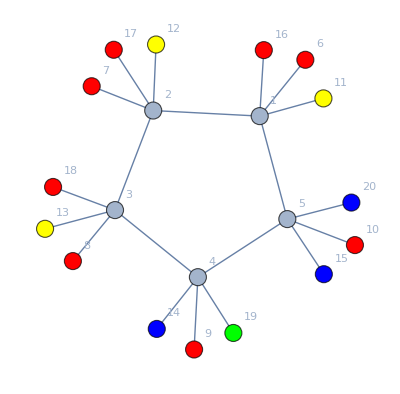

```mathematica
Graph[hairy,VertexStyle->AssignColors6[{1,1,1,1,1,4,4,4,3,3,1,1,1,2,3},Range[6,20]],VertexSize->Large,VertexLabels->"Name", GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
1,1,1,1,1,4,4,4,3,3,1,1,1,2,3
```

```mathematica
AbsoluteTiming[
TableForm[
Monitor[
Table[CountSolutions6[CycleGraph[5],{1<->3,1<->4},{2<->4,2<->5},{3<->5},k,Range[5]],{k,0,1024-1}],k], TableDepth->2
]
]
```

{225.798,0 | {1,1,1,1,1} | {0,0,0,0,0,0,0}
1 | {1,1,1,1,2} | {0,0,0,0,0,0,0}
2 | {1,1,1,1,3} | {0,0,0,0,0,0,0}
3 | {1,1,1,1,4} | {0,0,0,0,0,0,0}
4 | {1,1,1,2,1} | {0,0,0,0,0,0,0}
5 | {1,1,1,2,2} | {0,0,0,0,0,0,0}
6 | {1,1,1,2,3} | {0,0,0,0,0,0,0}
7 | {1,1,1,2,4} | {0,0,0,0,0,0,0}
8 | {1,1,1,3,1} | {0,0,0,0,0,0,0}
9 | {1,1,1,3,2} | {0,0,0,0,0,0,0}
10 | {1,1,1,3,3} | {0,0,0,0,0,0,0}
11 | {1,1,1,3,4} | {0,0,0,0,0,0,0}
12 | {1,1,1,4,1} | {0,0,0,0,0,0,0}
13 | {1,1,1,4,2} | {0,0,0,0,0,0,0}
14 | {1,1,1,4,3} | {0,0,0,0,0,0,0}
15 | {1,1,1,4,4} | {0,0,0,0,0,0,0}
16 | {1,1,2,1,1} | {0,0,0,0,0,0,0}
17 | {1,1,2,1,2} | {0,0,0,0,0,0,0}
18 | {1,1,2,1,3} | {0,0,0,0,0,0,0}
19 | {1,1,2,1,4} | {0,0,0,0,0,0,0}
20 | {1,1,2,2,1} | {0,0,0,0,0,0,0}
21 | {1,1,2,2,2} | {0,0,0,0,0,0,0}
22 | {1,1,2,2,3} | {0,0,0,0,0,0,0}
23 | {1,1,2,2,4} | {0,0,0,0,0,0,0}
24 | {1,1,2,3,1} | {0,0,0,0,0,0,0}
25 | {1,1,2,3,2} | {0,0,0,0,0,0,0}
26 | {1,1,2,3,3} | {0,0,0,0,0,0,0}
27 | {1,1,2,3,4} | {0,0,0,0,0,0,0}
28 | {1,1,2,4,1} | {0,0,0,0,0,0,0}
29 | {1,1,2,4,2} | {0,0,0,0,0,0,0}
30 | {1,1,2,4,3} | {0,0,0,0,0,0,0}
31 | {1,1,2,4,4} | {0,0,0,0,0,0,0}
32 | {1,1,3,1,1} | {0,0,0,0,0,0,0}
33 | {1,1,3,1,2} | {0,0,0,0,0,0,0}
34 | {1,1,3,1,3} | {0,0,0,0,0,0,0}
35 | {1,1,3,1,4} | {0,0,0,0,0,0,0}
36 | {1,1,3,2,1} | {0,0,0,0,0,0,0}
37 | {1,1,3,2,2} | {0,0,0,0,0,0,0}
38 | {1,1,3,2,3} | {0,0,0,0,0,0,0}
39 | {1,1,3,2,4} | {0,0,0,0,0,0,0}
40 | {1,1,3,3,1} | {0,0,0,0,0,0,0}
41 | {1,1,3,3,2} | {0,0,0,0,0,0,0}
42 | {1,1,3,3,3} | {0,0,0,0,0,0,0}
43 | {1,1,3,3,4} | {0,0,0,0,0,0,0}
44 | {1,1,3,4,1} | {0,0,0,0,0,0,0}
45 | {1,1,3,4,2} | {0,0,0,0,0,0,0}
46 | {1,1,3,4,3} | {0,0,0,0,0,0,0}
47 | {1,1,3,4,4} | {0,0,0,0,0,0,0}
48 | {1,1,4,1,1} | {0,0,0,0,0,0,0}
49 | {1,1,4,1,2} | {0,0,0,0,0,0,0}
50 | {1,1,4,1,3} | {0,0,0,0,0,0,0}
51 | {1,1,4,1,4} | {0,0,0,0,0,0,0}
52 | {1,1,4,2,1} | {0,0,0,0,0,0,0}
53 | {1,1,4,2,2} | {0,0,0,0,0,0,0}
54 | {1,1,4,2,3} | {0,0,0,0,0,0,0}
55 | {1,1,4,2,4} | {0,0,0,0,0,0,0}
56 | {1,1,4,3,1} | {0,0,0,0,0,0,0}
57 | {1,1,4,3,2} | {0,0,0,0,0,0,0}
58 | {1,1,4,3,3} | {0,0,0,0,0,0,0}
59 | {1,1,4,3,4} | {0,0,0,0,0,0,0}
60 | {1,1,4,4,1} | {0,0,0,0,0,0,0}
61 | {1,1,4,4,2} | {0,0,0,0,0,0,0}
62 | {1,1,4,4,3} | {0,0,0,0,0,0,0}
63 | {1,1,4,4,4} | {0,0,0,0,0,0,0}
64 | {1,2,1,1,1} | {0,0,0,0,0,0,0}
65 | {1,2,1,1,2} | {0,0,0,0,0,0,0}
66 | {1,2,1,1,3} | {0,0,0,0,0,0,0}
67 | {1,2,1,1,4} | {0,0,0,0,0,0,0}
68 | {1,2,1,2,1} | {0,0,0,0,0,0,0}
69 | {1,2,1,2,2} | {0,0,0,0,0,0,0}
70 | {1,2,1,2,3} | {0,0,1,0,0,0,0}
71 | {1,2,1,2,4} | {0,0,1,0,0,0,0}
72 | {1,2,1,3,1} | {0,0,0,0,0,0,0}
73 | {1,2,1,3,2} | {0,0,1,0,0,0,0}
74 | {1,2,1,3,3} | {0,0,0,0,0,0,0}
75 | {1,2,1,3,4} | {0,0,0,0,1,0,0}
76 | {1,2,1,4,1} | {0,0,0,0,0,0,0}
77 | {1,2,1,4,2} | {0,0,1,0,0,0,0}
78 | {1,2,1,4,3} | {0,0,0,0,1,0,0}
79 | {1,2,1,4,4} | {0,0,0,0,0,0,0}
80 | {1,2,2,1,1} | {0,0,0,0,0,0,0}
81 | {1,2,2,1,2} | {0,0,0,0,0,0,0}
82 | {1,2,2,1,3} | {0,0,0,0,0,0,0}
83 | {1,2,2,1,4} | {0,0,0,0,0,0,0}
84 | {1,2,2,2,1} | {0,0,0,0,0,0,0}
85 | {1,2,2,2,2} | {0,0,0,0,0,0,0}
86 | {1,2,2,2,3} | {0,0,0,0,0,0,0}
87 | {1,2,2,2,4} | {0,0,0,0,0,0,0}
88 | {1,2,2,3,1} | {0,0,0,0,0,0,0}
89 | {1,2,2,3,2} | {0,0,0,0,0,0,0}
90 | {1,2,2,3,3} | {0,0,0,0,0,0,0}
91 | {1,2,2,3,4} | {0,0,0,0,0,0,0}
92 | {1,2,2,4,1} | {0,0,0,0,0,0,0}
93 | {1,2,2,4,2} | {0,0,0,0,0,0,0}
94 | {1,2,2,4,3} | {0,0,0,0,0,0,0}
95 | {1,2,2,4,4} | {0,0,0,0,0,0,0}
96 | {1,2,3,1,1} | {0,0,0,0,0,0,0}
97 | {1,2,3,1,2} | {0,0,1,0,0,0,0}
98 | {1,2,3,1,3} | {0,1,0,0,0,0,0}
99 | {1,2,3,1,4} | {0,0,0,0,1,0,0}
100 | {1,2,3,2,1} | {0,0,0,0,0,0,0}
101 | {1,2,3,2,2} | {0,0,0,0,0,0,0}
102 | {1,2,3,2,3} | {1,0,0,0,0,0,0}
103 | {1,2,3,2,4} | {0,0,0,0,0,1,0}
104 | {1,2,3,3,1} | {0,0,0,0,0,0,0}
105 | {1,2,3,3,2} | {0,0,0,0,0,0,0}
106 | {1,2,3,3,3} | {0,0,0,0,0,0,0}
107 | {1,2,3,3,4} | {0,0,0,0,0,0,0}
108 | {1,2,3,4,1} | {0,0,0,0,0,0,0}
109 | {1,2,3,4,2} | {0,0,0,0,0,1,0}
110 | {1,2,3,4,3} | {0,0,0,1,0,0,0}
111 | {1,2,3,4,4} | {0,0,0,0,0,0,0}
112 | {1,2,4,1,1} | {0,0,0,0,0,0,0}
113 | {1,2,4,1,2} | {0,0,1,0,0,0,0}
114 | {1,2,4,1,3} | {0,0,0,0,1,0,0}
115 | {1,2,4,1,4} | {0,1,0,0,0,0,0}
116 | {1,2,4,2,1} | {0,0,0,0,0,0,0}
117 | {1,2,4,2,2} | {0,0,0,0,0,0,0}
118 | {1,2,4,2,3} | {0,0,0,0,0,1,0}
119 | {1,2,4,2,4} | {1,0,0,0,0,0,0}
120 | {1,2,4,3,1} | {0,0,0,0,0,0,0}
121 | {1,2,4,3,2} | {0,0,0,0,0,1,0}
122 | {1,2,4,3,3} | {0,0,0,0,0,0,0}
123 | {1,2,4,3,4} | {0,0,0,1,0,0,0}
124 | {1,2,4,4,1} | {0,0,0,0,0,0,0}
125 | {1,2,4,4,2} | {0,0,0,0,0,0,0}
126 | {1,2,4,4,3} | {0,0,0,0,0,0,0}
127 | {1,2,4,4,4} | {0,0,0,0,0,0,0}
128 | {1,3,1,1,1} | {0,0,0,0,0,0,0}
129 | {1,3,1,1,2} | {0,0,0,0,0,0,0}
130 | {1,3,1,1,3} | {0,0,0,0,0,0,0}
131 | {1,3,1,1,4} | {0,0,0,0,0,0,0}
132 | {1,3,1,2,1} | {0,0,0,0,0,0,0}
133 | {1,3,1,2,2} | {0,0,0,0,0,0,0}
134 | {1,3,1,2,3} | {0,0,1,0,0,0,0}
135 | {1,3,1,2,4} | {0,0,0,0,1,0,0}
136 | {1,3,1,3,1} | {0,0,0,0,0,0,0}
137 | {1,3,1,3,2} | {0,0,1,0,0,0,0}
138 | {1,3,1,3,3} | {0,0,0,0,0,0,0}
139 | {1,3,1,3,4} | {0,0,1,0,0,0,0}
140 | {1,3,1,4,1} | {0,0,0,0,0,0,0}
141 | {1,3,1,4,2} | {0,0,0,0,1,0,0}
142 | {1,3,1,4,3} | {0,0,1,0,0,0,0}
143 | {1,3,1,4,4} | {0,0,0,0,0,0,0}
144 | {1,3,2,1,1} | {0,0,0,0,0,0,0}
145 | {1,3,2,1,2} | {0,1,0,0,0,0,0}
146 | {1,3,2,1,3} | {0,0,1,0,0,0,0}
147 | {1,3,2,1,4} | {0,0,0,0,1,0,0}
148 | {1,3,2,2,1} | {0,0,0,0,0,0,0}
149 | {1,3,2,2,2} | {0,0,0,0,0,0,0}
150 | {1,3,2,2,3} | {0,0,0,0,0,0,0}
151 | {1,3,2,2,4} | {0,0,0,0,0,0,0}
152 | {1,3,2,3,1} | {0,0,0,0,0,0,0}
153 | {1,3,2,3,2} | {1,0,0,0,0,0,0}
154 | {1,3,2,3,3} | {0,0,0,0,0,0,0}
155 | {1,3,2,3,4} | {0,0,0,0,0,1,0}
156 | {1,3,2,4,1} | {0,0,0,0,0,0,0}
157 | {1,3,2,4,2} | {0,0,0,1,0,0,0}
158 | {1,3,2,4,3} | {0,0,0,0,0,1,0}
159 | {1,3,2,4,4} | {0,0,0,0,0,0,0}
160 | {1,3,3,1,1} | {0,0,0,0,0,0,0}
161 | {1,3,3,1,2} | {0,0,0,0,0,0,0}
162 | {1,3,3,1,3} | {0,0,0,0,0,0,0}
163 | {1,3,3,1,4} | {0,0,0,0,0,0,0}
164 | {1,3,3,2,1} | {0,0,0,0,0,0,0}
165 | {1,3,3,2,2} | {0,0,0,0,0,0,0}
166 | {1,3,3,2,3} | {0,0,0,0,0,0,0}
167 | {1,3,3,2,4} | {0,0,0,0,0,0,0}
168 | {1,3,3,3,1} | {0,0,0,0,0,0,0}
169 | {1,3,3,3,2} | {0,0,0,0,0,0,0}
170 | {1,3,3,3,3} | {0,0,0,0,0,0,0}
171 | {1,3,3,3,4} | {0,0,0,0,0,0,0}
172 | {1,3,3,4,1} | {0,0,0,0,0,0,0}
173 | {1,3,3,4,2} | {0,0,0,0,0,0,0}
174 | {1,3,3,4,3} | {0,0,0,0,0,0,0}
175 | {1,3,3,4,4} | {0,0,0,0,0,0,0}
176 | {1,3,4,1,1} | {0,0,0,0,0,0,0}
177 | {1,3,4,1,2} | {0,0,0,0,1,0,0}
178 | {1,3,4,1,3} | {0,0,1,0,0,0,0}
179 | {1,3,4,1,4} | {0,1,0,0,0,0,0}
180 | {1,3,4,2,1} | {0,0,0,0,0,0,0}
181 | {1,3,4,2,2} | {0,0,0,0,0,0,0}
182 | {1,3,4,2,3} | {0,0,0,0,0,1,0}
183 | {1,3,4,2,4} | {0,0,0,1,0,0,0}
184 | {1,3,4,3,1} | {0,0,0,0,0,0,0}
185 | {1,3,4,3,2} | {0,0,0,0,0,1,0}
186 | {1,3,4,3,3} | {0,0,0,0,0,0,0}
187 | {1,3,4,3,4} | {1,0,0,0,0,0,0}
188 | {1,3,4,4,1} | {0,0,0,0,0,0,0}
189 | {1,3,4,4,2} | {0,0,0,0,0,0,0}
190 | {1,3,4,4,3} | {0,0,0,0,0,0,0}
191 | {1,3,4,4,4} | {0,0,0,0,0,0,0}
192 | {1,4,1,1,1} | {0,0,0,0,0,0,0}
193 | {1,4,1,1,2} | {0,0,0,0,0,0,0}
194 | {1,4,1,1,3} | {0,0,0,0,0,0,0}
195 | {1,4,1,1,4} | {0,0,0,0,0,0,0}
196 | {1,4,1,2,1} | {0,0,0,0,0,0,0}
197 | {1,4,1,2,2} | {0,0,0,0,0,0,0}
198 | {1,4,1,2,3} | {0,0,0,0,1,0,0}
199 | {1,4,1,2,4} | {0,0,1,0,0,0,0}
200 | {1,4,1,3,1} | {0,0,0,0,0,0,0}
201 | {1,4,1,3,2} | {0,0,0,0,1,0,0}
202 | {1,4,1,3,3} | {0,0,0,0,0,0,0}
203 | {1,4,1,3,4} | {0,0,1,0,0,0,0}
204 | {1,4,1,4,1} | {0,0,0,0,0,0,0}
205 | {1,4,1,4,2} | {0,0,1,0,0,0,0}
206 | {1,4,1,4,3} | {0,0,1,0,0,0,0}
207 | {1,4,1,4,4} | {0,0,0,0,0,0,0}
208 | {1,4,2,1,1} | {0,0,0,0,0,0,0}
209 | {1,4,2,1,2} | {0,1,0,0,0,0,0}
210 | {1,4,2,1,3} | {0,0,0,0,1,0,0}
211 | {1,4,2,1,4} | {0,0,1,0,0,0,0}
212 | {1,4,2,2,1} | {0,0,0,0,0,0,0}
213 | {1,4,2,2,2} | {0,0,0,0,0,0,0}
214 | {1,4,2,2,3} | {0,0,0,0,0,0,0}
215 | {1,4,2,2,4} | {0,0,0,0,0,0,0}
216 | {1,4,2,3,1} | {0,0,0,0,0,0,0}
217 | {1,4,2,3,2} | {0,0,0,1,0,0,0}
218 | {1,4,2,3,3} | {0,0,0,0,0,0,0}
219 | {1,4,2,3,4} | {0,0,0,0,0,1,0}
220 | {1,4,2,4,1} | {0,0,0,0,0,0,0}
221 | {1,4,2,4,2} | {1,0,0,0,0,0,0}
222 | {1,4,2,4,3} | {0,0,0,0,0,1,0}
223 | {1,4,2,4,4} | {0,0,0,0,0,0,0}
224 | {1,4,3,1,1} | {0,0,0,0,0,0,0}
225 | {1,4,3,1,2} | {0,0,0,0,1,0,0}
226 | {1,4,3,1,3} | {0,1,0,0,0,0,0}
227 | {1,4,3,1,4} | {0,0,1,0,0,0,0}
228 | {1,4,3,2,1} | {0,0,0,0,0,0,0}
229 | {1,4,3,2,2} | {0,0,0,0,0,0,0}
230 | {1,4,3,2,3} | {0,0,0,1,0,0,0}
231 | {1,4,3,2,4} | {0,0,0,0,0,1,0}
232 | {1,4,3,3,1} | {0,0,0,0,0,0,0}
233 | {1,4,3,3,2} | {0,0,0,0,0,0,0}
234 | {1,4,3,3,3} | {0,0,0,0,0,0,0}
235 | {1,4,3,3,4} | {0,0,0,0,0,0,0}
236 | {1,4,3,4,1} | {0,0,0,0,0,0,0}
237 | {1,4,3,4,2} | {0,0,0,0,0,1,0}
238 | {1,4,3,4,3} | {1,0,0,0,0,0,0}
239 | {1,4,3,4,4} | {0,0,0,0,0,0,0}
240 | {1,4,4,1,1} | {0,0,0,0,0,0,0}
241 | {1,4,4,1,2} | {0,0,0,0,0,0,0}
242 | {1,4,4,1,3} | {0,0,0,0,0,0,0}
243 | {1,4,4,1,4} | {0,0,0,0,0,0,0}
244 | {1,4,4,2,1} | {0,0,0,0,0,0,0}
245 | {1,4,4,2,2} | {0,0,0,0,0,0,0}
246 | {1,4,4,2,3} | {0,0,0,0,0,0,0}
247 | {1,4,4,2,4} | {0,0,0,0,0,0,0}
248 | {1,4,4,3,1} | {0,0,0,0,0,0,0}
249 | {1,4,4,3,2} | {0,0,0,0,0,0,0}
250 | {1,4,4,3,3} | {0,0,0,0,0,0,0}
251 | {1,4,4,3,4} | {0,0,0,0,0,0,0}
252 | {1,4,4,4,1} | {0,0,0,0,0,0,0}
253 | {1,4,4,4,2} | {0,0,0,0,0,0,0}
254 | {1,4,4,4,3} | {0,0,0,0,0,0,0}
255 | {1,4,4,4,4} | {0,0,0,0,0,0,0}
256 | {2,1,1,1,1} | {0,0,0,0,0,0,0}
257 | {2,1,1,1,2} | {0,0,0,0,0,0,0}
258 | {2,1,1,1,3} | {0,0,0,0,0,0,0}
259 | {2,1,1,1,4} | {0,0,0,0,0,0,0}
260 | {2,1,1,2,1} | {0,0,0,0,0,0,0}
261 | {2,1,1,2,2} | {0,0,0,0,0,0,0}
262 | {2,1,1,2,3} | {0,0,0,0,0,0,0}
263 | {2,1,1,2,4} | {0,0,0,0,0,0,0}
264 | {2,1,1,3,1} | {0,0,0,0,0,0,0}
265 | {2,1,1,3,2} | {0,0,0,0,0,0,0}
266 | {2,1,1,3,3} | {0,0,0,0,0,0,0}
267 | {2,1,1,3,4} | {0,0,0,0,0,0,0}
268 | {2,1,1,4,1} | {0,0,0,0,0,0,0}
269 | {2,1,1,4,2} | {0,0,0,0,0,0,0}
270 | {2,1,1,4,3} | {0,0,0,0,0,0,0}
271 | {2,1,1,4,4} | {0,0,0,0,0,0,0}
272 | {2,1,2,1,1} | {0,0,0,0,0,0,0}
273 | {2,1,2,1,2} | {0,0,0,0,0,0,0}
274 | {2,1,2,1,3} | {0,0,1,0,0,0,0}
275 | {2,1,2,1,4} | {0,0,1,0,0,0,0}
276 | {2,1,2,2,1} | {0,0,0,0,0,0,0}
277 | {2,1,2,2,2} | {0,0,0,0,0,0,0}
278 | {2,1,2,2,3} | {0,0,0,0,0,0,0}
279 | {2,1,2,2,4} | {0,0,0,0,0,0,0}
280 | {2,1,2,3,1} | {0,0,1,0,0,0,0}
281 | {2,1,2,3,2} | {0,0,0,0,0,0,0}
282 | {2,1,2,3,3} | {0,0,0,0,0,0,0}
283 | {2,1,2,3,4} | {0,0,0,0,1,0,0}
284 | {2,1,2,4,1} | {0,0,1,0,0,0,0}
285 | {2,1,2,4,2} | {0,0,0,0,0,0,0}
286 | {2,1,2,4,3} | {0,0,0,0,1,0,0}
287 | {2,1,2,4,4} | {0,0,0,0,0,0,0}
288 | {2,1,3,1,1} | {0,0,0,0,0,0,0}
289 | {2,1,3,1,2} | {0,0,0,0,0,0,0}
290 | {2,1,3,1,3} | {1,0,0,0,0,0,0}
291 | {2,1,3,1,4} | {0,0,0,0,0,1,0}
292 | {2,1,3,2,1} | {0,0,1,0,0,0,0}
293 | {2,1,3,2,2} | {0,0,0,0,0,0,0}
294 | {2,1,3,2,3} | {0,1,0,0,0,0,0}
295 | {2,1,3,2,4} | {0,0,0,0,1,0,0}
296 | {2,1,3,3,1} | {0,0,0,0,0,0,0}
297 | {2,1,3,3,2} | {0,0,0,0,0,0,0}
298 | {2,1,3,3,3} | {0,0,0,0,0,0,0}
299 | {2,1,3,3,4} | {0,0,0,0,0,0,0}
300 | {2,1,3,4,1} | {0,0,0,0,0,1,0}
301 | {2,1,3,4,2} | {0,0,0,0,0,0,0}
302 | {2,1,3,4,3} | {0,0,0,1,0,0,0}
303 | {2,1,3,4,4} | {0,0,0,0,0,0,0}
304 | {2,1,4,1,1} | {0,0,0,0,0,0,0}
305 | {2,1,4,1,2} | {0,0,0,0,0,0,0}
306 | {2,1,4,1,3} | {0,0,0,0,0,1,0}
307 | {2,1,4,1,4} | {1,0,0,0,0,0,0}
308 | {2,1,4,2,1} | {0,0,1,0,0,0,0}
309 | {2,1,4,2,2} | {0,0,0,0,0,0,0}
310 | {2,1,4,2,3} | {0,0,0,0,1,0,0}
311 | {2,1,4,2,4} | {0,1,0,0,0,0,0}
312 | {2,1,4,3,1} | {0,0,0,0,0,1,0}
313 | {2,1,4,3,2} | {0,0,0,0,0,0,0}
314 | {2,1,4,3,3} | {0,0,0,0,0,0,0}
315 | {2,1,4,3,4} | {0,0,0,1,0,0,0}
316 | {2,1,4,4,1} | {0,0,0,0,0,0,0}
317 | {2,1,4,4,2} | {0,0,0,0,0,0,0}
318 | {2,1,4,4,3} | {0,0,0,0,0,0,0}
319 | {2,1,4,4,4} | {0,0,0,0,0,0,0}
320 | {2,2,1,1,1} | {0,0,0,0,0,0,0}
321 | {2,2,1,1,2} | {0,0,0,0,0,0,0}
322 | {2,2,1,1,3} | {0,0,0,0,0,0,0}
323 | {2,2,1,1,4} | {0,0,0,0,0,0,0}
324 | {2,2,1,2,1} | {0,0,0,0,0,0,0}
325 | {2,2,1,2,2} | {0,0,0,0,0,0,0}
326 | {2,2,1,2,3} | {0,0,0,0,0,0,0}
327 | {2,2,1,2,4} | {0,0,0,0,0,0,0}
328 | {2,2,1,3,1} | {0,0,0,0,0,0,0}
329 | {2,2,1,3,2} | {0,0,0,0,0,0,0}
330 | {2,2,1,3,3} | {0,0,0,0,0,0,0}
331 | {2,2,1,3,4} | {0,0,0,0,0,0,0}
332 | {2,2,1,4,1} | {0,0,0,0,0,0,0}
333 | {2,2,1,4,2} | {0,0,0,0,0,0,0}
334 | {2,2,1,4,3} | {0,0,0,0,0,0,0}
335 | {2,2,1,4,4} | {0,0,0,0,0,0,0}
336 | {2,2,2,1,1} | {0,0,0,0,0,0,0}
337 | {2,2,2,1,2} | {0,0,0,0,0,0,0}
338 | {2,2,2,1,3} | {0,0,0,0,0,0,0}
339 | {2,2,2,1,4} | {0,0,0,0,0,0,0}
340 | {2,2,2,2,1} | {0,0,0,0,0,0,0}
341 | {2,2,2,2,2} | {0,0,0,0,0,0,0}
342 | {2,2,2,2,3} | {0,0,0,0,0,0,0}
343 | {2,2,2,2,4} | {0,0,0,0,0,0,0}
344 | {2,2,2,3,1} | {0,0,0,0,0,0,0}
345 | {2,2,2,3,2} | {0,0,0,0,0,0,0}
346 | {2,2,2,3,3} | {0,0,0,0,0,0,0}
347 | {2,2,2,3,4} | {0,0,0,0,0,0,0}
348 | {2,2,2,4,1} | {0,0,0,0,0,0,0}
349 | {2,2,2,4,2} | {0,0,0,0,0,0,0}
350 | {2,2,2,4,3} | {0,0,0,0,0,0,0}
351 | {2,2,2,4,4} | {0,0,0,0,0,0,0}
352 | {2,2,3,1,1} | {0,0,0,0,0,0,0}
353 | {2,2,3,1,2} | {0,0,0,0,0,0,0}
354 | {2,2,3,1,3} | {0,0,0,0,0,0,0}
355 | {2,2,3,1,4} | {0,0,0,0,0,0,0}
356 | {2,2,3,2,1} | {0,0,0,0,0,0,0}
357 | {2,2,3,2,2} | {0,0,0,0,0,0,0}
358 | {2,2,3,2,3} | {0,0,0,0,0,0,0}
359 | {2,2,3,2,4} | {0,0,0,0,0,0,0}
360 | {2,2,3,3,1} | {0,0,0,0,0,0,0}
361 | {2,2,3,3,2} | {0,0,0,0,0,0,0}
362 | {2,2,3,3,3} | {0,0,0,0,0,0,0}
363 | {2,2,3,3,4} | {0,0,0,0,0,0,0}
364 | {2,2,3,4,1} | {0,0,0,0,0,0,0}
365 | {2,2,3,4,2} | {0,0,0,0,0,0,0}
366 | {2,2,3,4,3} | {0,0,0,0,0,0,0}
367 | {2,2,3,4,4} | {0,0,0,0,0,0,0}
368 | {2,2,4,1,1} | {0,0,0,0,0,0,0}
369 | {2,2,4,1,2} | {0,0,0,0,0,0,0}
370 | {2,2,4,1,3} | {0,0,0,0,0,0,0}
371 | {2,2,4,1,4} | {0,0,0,0,0,0,0}
372 | {2,2,4,2,1} | {0,0,0,0,0,0,0}
373 | {2,2,4,2,2} | {0,0,0,0,0,0,0}
374 | {2,2,4,2,3} | {0,0,0,0,0,0,0}
375 | {2,2,4,2,4} | {0,0,0,0,0,0,0}
376 | {2,2,4,3,1} | {0,0,0,0,0,0,0}
377 | {2,2,4,3,2} | {0,0,0,0,0,0,0}
378 | {2,2,4,3,3} | {0,0,0,0,0,0,0}
379 | {2,2,4,3,4} | {0,0,0,0,0,0,0}
380 | {2,2,4,4,1} | {0,0,0,0,0,0,0}
381 | {2,2,4,4,2} | {0,0,0,0,0,0,0}
382 | {2,2,4,4,3} | {0,0,0,0,0,0,0}
383 | {2,2,4,4,4} | {0,0,0,0,0,0,0}
384 | {2,3,1,1,1} | {0,0,0,0,0,0,0}
385 | {2,3,1,1,2} | {0,0,0,0,0,0,0}
386 | {2,3,1,1,3} | {0,0,0,0,0,0,0}
387 | {2,3,1,1,4} | {0,0,0,0,0,0,0}
388 | {2,3,1,2,1} | {0,1,0,0,0,0,0}
389 | {2,3,1,2,2} | {0,0,0,0,0,0,0}
390 | {2,3,1,2,3} | {0,0,1,0,0,0,0}
391 | {2,3,1,2,4} | {0,0,0,0,1,0,0}
392 | {2,3,1,3,1} | {1,0,0,0,0,0,0}
393 | {2,3,1,3,2} | {0,0,0,0,0,0,0}
394 | {2,3,1,3,3} | {0,0,0,0,0,0,0}
395 | {2,3,1,3,4} | {0,0,0,0,0,1,0}
396 | {2,3,1,4,1} | {0,0,0,1,0,0,0}
397 | {2,3,1,4,2} | {0,0,0,0,0,0,0}
398 | {2,3,1,4,3} | {0,0,0,0,0,1,0}
399 | {2,3,1,4,4} | {0,0,0,0,0,0,0}
400 | {2,3,2,1,1} | {0,0,0,0,0,0,0}
401 | {2,3,2,1,2} | {0,0,0,0,0,0,0}
402 | {2,3,2,1,3} | {0,0,1,0,0,0,0}
403 | {2,3,2,1,4} | {0,0,0,0,1,0,0}
404 | {2,3,2,2,1} | {0,0,0,0,0,0,0}
405 | {2,3,2,2,2} | {0,0,0,0,0,0,0}
406 | {2,3,2,2,3} | {0,0,0,0,0,0,0}
407 | {2,3,2,2,4} | {0,0,0,0,0,0,0}
408 | {2,3,2,3,1} | {0,0,1,0,0,0,0}
409 | {2,3,2,3,2} | {0,0,0,0,0,0,0}
410 | {2,3,2,3,3} | {0,0,0,0,0,0,0}
411 | {2,3,2,3,4} | {0,0,1,0,0,0,0}
412 | {2,3,2,4,1} | {0,0,0,0,1,0,0}
413 | {2,3,2,4,2} | {0,0,0,0,0,0,0}
414 | {2,3,2,4,3} | {0,0,1,0,0,0,0}
415 | {2,3,2,4,4} | {0,0,0,0,0,0,0}
416 | {2,3,3,1,1} | {0,0,0,0,0,0,0}
417 | {2,3,3,1,2} | {0,0,0,0,0,0,0}
418 | {2,3,3,1,3} | {0,0,0,0,0,0,0}
419 | {2,3,3,1,4} | {0,0,0,0,0,0,0}
420 | {2,3,3,2,1} | {0,0,0,0,0,0,0}
421 | {2,3,3,2,2} | {0,0,0,0,0,0,0}
422 | {2,3,3,2,3} | {0,0,0,0,0,0,0}
423 | {2,3,3,2,4} | {0,0,0,0,0,0,0}
424 | {2,3,3,3,1} | {0,0,0,0,0,0,0}
425 | {2,3,3,3,2} | {0,0,0,0,0,0,0}
426 | {2,3,3,3,3} | {0,0,0,0,0,0,0}
427 | {2,3,3,3,4} | {0,0,0,0,0,0,0}
428 | {2,3,3,4,1} | {0,0,0,0,0,0,0}
429 | {2,3,3,4,2} | {0,0,0,0,0,0,0}
430 | {2,3,3,4,3} | {0,0,0,0,0,0,0}
431 | {2,3,3,4,4} | {0,0,0,0,0,0,0}
432 | {2,3,4,1,1} | {0,0,0,0,0,0,0}
433 | {2,3,4,1,2} | {0,0,0,0,0,0,0}
434 | {2,3,4,1,3} | {0,0,0,0,0,1,0}
435 | {2,3,4,1,4} | {0,0,0,1,0,0,0}
436 | {2,3,4,2,1} | {0,0,0,0,1,0,0}
437 | {2,3,4,2,2} | {0,0,0,0,0,0,0}
438 | {2,3,4,2,3} | {0,0,1,0,0,0,0}
439 | {2,3,4,2,4} | {0,1,0,0,0,0,0}
440 | {2,3,4,3,1} | {0,0,0,0,0,1,0}
441 | {2,3,4,3,2} | {0,0,0,0,0,0,0}
442 | {2,3,4,3,3} | {0,0,0,0,0,0,0}
443 | {2,3,4,3,4} | {1,0,0,0,0,0,0}
444 | {2,3,4,4,1} | {0,0,0,0,0,0,0}
445 | {2,3,4,4,2} | {0,0,0,0,0,0,0}
446 | {2,3,4,4,3} | {0,0,0,0,0,0,0}
447 | {2,3,4,4,4} | {0,0,0,0,0,0,0}
448 | {2,4,1,1,1} | {0,0,0,0,0,0,0}
449 | {2,4,1,1,2} | {0,0,0,0,0,0,0}
450 | {2,4,1,1,3} | {0,0,0,0,0,0,0}
451 | {2,4,1,1,4} | {0,0,0,0,0,0,0}
452 | {2,4,1,2,1} | {0,1,0,0,0,0,0}
453 | {2,4,1,2,2} | {0,0,0,0,0,0,0}
454 | {2,4,1,2,3} | {0,0,0,0,1,0,0}
455 | {2,4,1,2,4} | {0,0,1,0,0,0,0}
456 | {2,4,1,3,1} | {0,0,0,1,0,0,0}
457 | {2,4,1,3,2} | {0,0,0,0,0,0,0}
458 | {2,4,1,3,3} | {0,0,0,0,0,0,0}
459 | {2,4,1,3,4} | {0,0,0,0,0,1,0}
460 | {2,4,1,4,1} | {1,0,0,0,0,0,0}
461 | {2,4,1,4,2} | {0,0,0,0,0,0,0}
462 | {2,4,1,4,3} | {0,0,0,0,0,1,0}
463 | {2,4,1,4,4} | {0,0,0,0,0,0,0}
464 | {2,4,2,1,1} | {0,0,0,0,0,0,0}
465 | {2,4,2,1,2} | {0,0,0,0,0,0,0}
466 | {2,4,2,1,3} | {0,0,0,0,1,0,0}
467 | {2,4,2,1,4} | {0,0,1,0,0,0,0}
468 | {2,4,2,2,1} | {0,0,0,0,0,0,0}
469 | {2,4,2,2,2} | {0,0,0,0,0,0,0}
470 | {2,4,2,2,3} | {0,0,0,0,0,0,0}
471 | {2,4,2,2,4} | {0,0,0,0,0,0,0}
472 | {2,4,2,3,1} | {0,0,0,0,1,0,0}
473 | {2,4,2,3,2} | {0,0,0,0,0,0,0}
474 | {2,4,2,3,3} | {0,0,0,0,0,0,0}
475 | {2,4,2,3,4} | {0,0,1,0,0,0,0}
476 | {2,4,2,4,1} | {0,0,1,0,0,0,0}
477 | {2,4,2,4,2} | {0,0,0,0,0,0,0}
478 | {2,4,2,4,3} | {0,0,1,0,0,0,0}
479 | {2,4,2,4,4} | {0,0,0,0,0,0,0}
480 | {2,4,3,1,1} | {0,0,0,0,0,0,0}
481 | {2,4,3,1,2} | {0,0,0,0,0,0,0}
482 | {2,4,3,1,3} | {0,0,0,1,0,0,0}
483 | {2,4,3,1,4} | {0,0,0,0,0,1,0}
484 | {2,4,3,2,1} | {0,0,0,0,1,0,0}
485 | {2,4,3,2,2} | {0,0,0,0,0,0,0}
486 | {2,4,3,2,3} | {0,1,0,0,0,0,0}
487 | {2,4,3,2,4} | {0,0,1,0,0,0,0}
488 | {2,4,3,3,1} | {0,0,0,0,0,0,0}
489 | {2,4,3,3,2} | {0,0,0,0,0,0,0}
490 | {2,4,3,3,3} | {0,0,0,0,0,0,0}
491 | {2,4,3,3,4} | {0,0,0,0,0,0,0}
492 | {2,4,3,4,1} | {0,0,0,0,0,1,0}
493 | {2,4,3,4,2} | {0,0,0,0,0,0,0}
494 | {2,4,3,4,3} | {1,0,0,0,0,0,0}
495 | {2,4,3,4,4} | {0,0,0,0,0,0,0}
496 | {2,4,4,1,1} | {0,0,0,0,0,0,0}
497 | {2,4,4,1,2} | {0,0,0,0,0,0,0}
498 | {2,4,4,1,3} | {0,0,0,0,0,0,0}
499 | {2,4,4,1,4} | {0,0,0,0,0,0,0}
500 | {2,4,4,2,1} | {0,0,0,0,0,0,0}
501 | {2,4,4,2,2} | {0,0,0,0,0,0,0}
502 | {2,4,4,2,3} | {0,0,0,0,0,0,0}
503 | {2,4,4,2,4} | {0,0,0,0,0,0,0}
504 | {2,4,4,3,1} | {0,0,0,0,0,0,0}
505 | {2,4,4,3,2} | {0,0,0,0,0,0,0}
506 | {2,4,4,3,3} | {0,0,0,0,0,0,0}
507 | {2,4,4,3,4} | {0,0,0,0,0,0,0}
508 | {2,4,4,4,1} | {0,0,0,0,0,0,0}
509 | {2,4,4,4,2} | {0,0,0,0,0,0,0}
510 | {2,4,4,4,3} | {0,0,0,0,0,0,0}
511 | {2,4,4,4,4} | {0,0,0,0,0,0,0}
512 | {3,1,1,1,1} | {0,0,0,0,0,0,0}
513 | {3,1,1,1,2} | {0,0,0,0,0,0,0}
514 | {3,1,1,1,3} | {0,0,0,0,0,0,0}
515 | {3,1,1,1,4} | {0,0,0,0,0,0,0}
516 | {3,1,1,2,1} | {0,0,0,0,0,0,0}
517 | {3,1,1,2,2} | {0,0,0,0,0,0,0}
518 | {3,1,1,2,3} | {0,0,0,0,0,0,0}
519 | {3,1,1,2,4} | {0,0,0,0,0,0,0}
520 | {3,1,1,3,1} | {0,0,0,0,0,0,0}
521 | {3,1,1,3,2} | {0,0,0,0,0,0,0}
522 | {3,1,1,3,3} | {0,0,0,0,0,0,0}
523 | {3,1,1,3,4} | {0,0,0,0,0,0,0}
524 | {3,1,1,4,1} | {0,0,0,0,0,0,0}
525 | {3,1,1,4,2} | {0,0,0,0,0,0,0}
526 | {3,1,1,4,3} | {0,0,0,0,0,0,0}
527 | {3,1,1,4,4} | {0,0,0,0,0,0,0}
528 | {3,1,2,1,1} | {0,0,0,0,0,0,0}
529 | {3,1,2,1,2} | {1,0,0,0,0,0,0}
530 | {3,1,2,1,3} | {0,0,0,0,0,0,0}
531 | {3,1,2,1,4} | {0,0,0,0,0,1,0}
532 | {3,1,2,2,1} | {0,0,0,0,0,0,0}
533 | {3,1,2,2,2} | {0,0,0,0,0,0,0}
534 | {3,1,2,2,3} | {0,0,0,0,0,0,0}
535 | {3,1,2,2,4} | {0,0,0,0,0,0,0}
536 | {3,1,2,3,1} | {0,0,1,0,0,0,0}
537 | {3,1,2,3,2} | {0,1,0,0,0,0,0}
538 | {3,1,2,3,3} | {0,0,0,0,0,0,0}
539 | {3,1,2,3,4} | {0,0,0,0,1,0,0}
540 | {3,1,2,4,1} | {0,0,0,0,0,1,0}
541 | {3,1,2,4,2} | {0,0,0,1,0,0,0}
542 | {3,1,2,4,3} | {0,0,0,0,0,0,0}
543 | {3,1,2,4,4} | {0,0,0,0,0,0,0}
544 | {3,1,3,1,1} | {0,0,0,0,0,0,0}
545 | {3,1,3,1,2} | {0,0,1,0,0,0,0}
546 | {3,1,3,1,3} | {0,0,0,0,0,0,0}
547 | {3,1,3,1,4} | {0,0,1,0,0,0,0}
548 | {3,1,3,2,1} | {0,0,1,0,0,0,0}
549 | {3,1,3,2,2} | {0,0,0,0,0,0,0}
550 | {3,1,3,2,3} | {0,0,0,0,0,0,0}
551 | {3,1,3,2,4} | {0,0,0,0,1,0,0}
552 | {3,1,3,3,1} | {0,0,0,0,0,0,0}
553 | {3,1,3,3,2} | {0,0,0,0,0,0,0}
554 | {3,1,3,3,3} | {0,0,0,0,0,0,0}
555 | {3,1,3,3,4} | {0,0,0,0,0,0,0}
556 | {3,1,3,4,1} | {0,0,1,0,0,0,0}
557 | {3,1,3,4,2} | {0,0,0,0,1,0,0}
558 | {3,1,3,4,3} | {0,0,0,0,0,0,0}
559 | {3,1,3,4,4} | {0,0,0,0,0,0,0}
560 | {3,1,4,1,1} | {0,0,0,0,0,0,0}
561 | {3,1,4,1,2} | {0,0,0,0,0,1,0}
562 | {3,1,4,1,3} | {0,0,0,0,0,0,0}
563 | {3,1,4,1,4} | {1,0,0,0,0,0,0}
564 | {3,1,4,2,1} | {0,0,0,0,0,1,0}
565 | {3,1,4,2,2} | {0,0,0,0,0,0,0}
566 | {3,1,4,2,3} | {0,0,0,0,0,0,0}
567 | {3,1,4,2,4} | {0,0,0,1,0,0,0}
568 | {3,1,4,3,1} | {0,0,1,0,0,0,0}
569 | {3,1,4,3,2} | {0,0,0,0,1,0,0}
570 | {3,1,4,3,3} | {0,0,0,0,0,0,0}
571 | {3,1,4,3,4} | {0,1,0,0,0,0,0}
572 | {3,1,4,4,1} | {0,0,0,0,0,0,0}
573 | {3,1,4,4,2} | {0,0,0,0,0,0,0}
574 | {3,1,4,4,3} | {0,0,0,0,0,0,0}
575 | {3,1,4,4,4} | {0,0,0,0,0,0,0}
576 | {3,2,1,1,1} | {0,0,0,0,0,0,0}
577 | {3,2,1,1,2} | {0,0,0,0,0,0,0}
578 | {3,2,1,1,3} | {0,0,0,0,0,0,0}
579 | {3,2,1,1,4} | {0,0,0,0,0,0,0}
580 | {3,2,1,2,1} | {1,0,0,0,0,0,0}
581 | {3,2,1,2,2} | {0,0,0,0,0,0,0}
582 | {3,2,1,2,3} | {0,0,0,0,0,0,0}
583 | {3,2,1,2,4} | {0,0,0,0,0,1,0}
584 | {3,2,1,3,1} | {0,1,0,0,0,0,0}
585 | {3,2,1,3,2} | {0,0,1,0,0,0,0}
586 | {3,2,1,3,3} | {0,0,0,0,0,0,0}
587 | {3,2,1,3,4} | {0,0,0,0,1,0,0}
588 | {3,2,1,4,1} | {0,0,0,1,0,0,0}
589 | {3,2,1,4,2} | {0,0,0,0,0,1,0}
590 | {3,2,1,4,3} | {0,0,0,0,0,0,0}
591 | {3,2,1,4,4} | {0,0,0,0,0,0,0}
592 | {3,2,2,1,1} | {0,0,0,0,0,0,0}
593 | {3,2,2,1,2} | {0,0,0,0,0,0,0}
594 | {3,2,2,1,3} | {0,0,0,0,0,0,0}
595 | {3,2,2,1,4} | {0,0,0,0,0,0,0}
596 | {3,2,2,2,1} | {0,0,0,0,0,0,0}
597 | {3,2,2,2,2} | {0,0,0,0,0,0,0}
598 | {3,2,2,2,3} | {0,0,0,0,0,0,0}
599 | {3,2,2,2,4} | {0,0,0,0,0,0,0}
600 | {3,2,2,3,1} | {0,0,0,0,0,0,0}
601 | {3,2,2,3,2} | {0,0,0,0,0,0,0}
602 | {3,2,2,3,3} | {0,0,0,0,0,0,0}
603 | {3,2,2,3,4} | {0,0,0,0,0,0,0}
604 | {3,2,2,4,1} | {0,0,0,0,0,0,0}
605 | {3,2,2,4,2} | {0,0,0,0,0,0,0}
606 | {3,2,2,4,3} | {0,0,0,0,0,0,0}
607 | {3,2,2,4,4} | {0,0,0,0,0,0,0}
608 | {3,2,3,1,1} | {0,0,0,0,0,0,0}
609 | {3,2,3,1,2} | {0,0,1,0,0,0,0}
610 | {3,2,3,1,3} | {0,0,0,0,0,0,0}
611 | {3,2,3,1,4} | {0,0,0,0,1,0,0}
612 | {3,2,3,2,1} | {0,0,1,0,0,0,0}
613 | {3,2,3,2,2} | {0,0,0,0,0,0,0}
614 | {3,2,3,2,3} | {0,0,0,0,0,0,0}
615 | {3,2,3,2,4} | {0,0,1,0,0,0,0}
616 | {3,2,3,3,1} | {0,0,0,0,0,0,0}
617 | {3,2,3,3,2} | {0,0,0,0,0,0,0}
618 | {3,2,3,3,3} | {0,0,0,0,0,0,0}
619 | {3,2,3,3,4} | {0,0,0,0,0,0,0}
620 | {3,2,3,4,1} | {0,0,0,0,1,0,0}
621 | {3,2,3,4,2} | {0,0,1,0,0,0,0}
622 | {3,2,3,4,3} | {0,0,0,0,0,0,0}
623 | {3,2,3,4,4} | {0,0,0,0,0,0,0}
624 | {3,2,4,1,1} | {0,0,0,0,0,0,0}
625 | {3,2,4,1,2} | {0,0,0,0,0,1,0}
626 | {3,2,4,1,3} | {0,0,0,0,0,0,0}
627 | {3,2,4,1,4} | {0,0,0,1,0,0,0}
628 | {3,2,4,2,1} | {0,0,0,0,0,1,0}
629 | {3,2,4,2,2} | {0,0,0,0,0,0,0}
630 | {3,2,4,2,3} | {0,0,0,0,0,0,0}
631 | {3,2,4,2,4} | {1,0,0,0,0,0,0}
632 | {3,2,4,3,1} | {0,0,0,0,1,0,0}
633 | {3,2,4,3,2} | {0,0,1,0,0,0,0}
634 | {3,2,4,3,3} | {0,0,0,0,0,0,0}
635 | {3,2,4,3,4} | {0,1,0,0,0,0,0}
636 | {3,2,4,4,1} | {0,0,0,0,0,0,0}
637 | {3,2,4,4,2} | {0,0,0,0,0,0,0}
638 | {3,2,4,4,3} | {0,0,0,0,0,0,0}
639 | {3,2,4,4,4} | {0,0,0,0,0,0,0}
640 | {3,3,1,1,1} | {0,0,0,0,0,0,0}
641 | {3,3,1,1,2} | {0,0,0,0,0,0,0}
642 | {3,3,1,1,3} | {0,0,0,0,0,0,0}
643 | {3,3,1,1,4} | {0,0,0,0,0,0,0}
644 | {3,3,1,2,1} | {0,0,0,0,0,0,0}
645 | {3,3,1,2,2} | {0,0,0,0,0,0,0}
646 | {3,3,1,2,3} | {0,0,0,0,0,0,0}
647 | {3,3,1,2,4} | {0,0,0,0,0,0,0}
648 | {3,3,1,3,1} | {0,0,0,0,0,0,0}
649 | {3,3,1,3,2} | {0,0,0,0,0,0,0}
650 | {3,3,1,3,3} | {0,0,0,0,0,0,0}
651 | {3,3,1,3,4} | {0,0,0,0,0,0,0}
652 | {3,3,1,4,1} | {0,0,0,0,0,0,0}
653 | {3,3,1,4,2} | {0,0,0,0,0,0,0}
654 | {3,3,1,4,3} | {0,0,0,0,0,0,0}
655 | {3,3,1,4,4} | {0,0,0,0,0,0,0}
656 | {3,3,2,1,1} | {0,0,0,0,0,0,0}
657 | {3,3,2,1,2} | {0,0,0,0,0,0,0}
658 | {3,3,2,1,3} | {0,0,0,0,0,0,0}
659 | {3,3,2,1,4} | {0,0,0,0,0,0,0}
660 | {3,3,2,2,1} | {0,0,0,0,0,0,0}
661 | {3,3,2,2,2} | {0,0,0,0,0,0,0}
662 | {3,3,2,2,3} | {0,0,0,0,0,0,0}
663 | {3,3,2,2,4} | {0,0,0,0,0,0,0}
664 | {3,3,2,3,1} | {0,0,0,0,0,0,0}
665 | {3,3,2,3,2} | {0,0,0,0,0,0,0}
666 | {3,3,2,3,3} | {0,0,0,0,0,0,0}
667 | {3,3,2,3,4} | {0,0,0,0,0,0,0}
668 | {3,3,2,4,1} | {0,0,0,0,0,0,0}
669 | {3,3,2,4,2} | {0,0,0,0,0,0,0}
670 | {3,3,2,4,3} | {0,0,0,0,0,0,0}
671 | {3,3,2,4,4} | {0,0,0,0,0,0,0}
672 | {3,3,3,1,1} | {0,0,0,0,0,0,0}
673 | {3,3,3,1,2} | {0,0,0,0,0,0,0}
674 | {3,3,3,1,3} | {0,0,0,0,0,0,0}
675 | {3,3,3,1,4} | {0,0,0,0,0,0,0}
676 | {3,3,3,2,1} | {0,0,0,0,0,0,0}
677 | {3,3,3,2,2} | {0,0,0,0,0,0,0}
678 | {3,3,3,2,3} | {0,0,0,0,0,0,0}
679 | {3,3,3,2,4} | {0,0,0,0,0,0,0}
680 | {3,3,3,3,1} | {0,0,0,0,0,0,0}
681 | {3,3,3,3,2} | {0,0,0,0,0,0,0}
682 | {3,3,3,3,3} | {0,0,0,0,0,0,0}
683 | {3,3,3,3,4} | {0,0,0,0,0,0,0}
684 | {3,3,3,4,1} | {0,0,0,0,0,0,0}
685 | {3,3,3,4,2} | {0,0,0,0,0,0,0}
686 | {3,3,3,4,3} | {0,0,0,0,0,0,0}
687 | {3,3,3,4,4} | {0,0,0,0,0,0,0}
688 | {3,3,4,1,1} | {0,0,0,0,0,0,0}
689 | {3,3,4,1,2} | {0,0,0,0,0,0,0}
690 | {3,3,4,1,3} | {0,0,0,0,0,0,0}
691 | {3,3,4,1,4} | {0,0,0,0,0,0,0}
692 | {3,3,4,2,1} | {0,0,0,0,0,0,0}
693 | {3,3,4,2,2} | {0,0,0,0,0,0,0}
694 | {3,3,4,2,3} | {0,0,0,0,0,0,0}
695 | {3,3,4,2,4} | {0,0,0,0,0,0,0}
696 | {3,3,4,3,1} | {0,0,0,0,0,0,0}
697 | {3,3,4,3,2} | {0,0,0,0,0,0,0}
698 | {3,3,4,3,3} | {0,0,0,0,0,0,0}
699 | {3,3,4,3,4} | {0,0,0,0,0,0,0}
700 | {3,3,4,4,1} | {0,0,0,0,0,0,0}
701 | {3,3,4,4,2} | {0,0,0,0,0,0,0}
702 | {3,3,4,4,3} | {0,0,0,0,0,0,0}
703 | {3,3,4,4,4} | {0,0,0,0,0,0,0}
704 | {3,4,1,1,1} | {0,0,0,0,0,0,0}
705 | {3,4,1,1,2} | {0,0,0,0,0,0,0}
706 | {3,4,1,1,3} | {0,0,0,0,0,0,0}
707 | {3,4,1,1,4} | {0,0,0,0,0,0,0}
708 | {3,4,1,2,1} | {0,0,0,1,0,0,0}
709 | {3,4,1,2,2} | {0,0,0,0,0,0,0}
710 | {3,4,1,2,3} | {0,0,0,0,0,0,0}
711 | {3,4,1,2,4} | {0,0,0,0,0,1,0}
712 | {3,4,1,3,1} | {0,1,0,0,0,0,0}
713 | {3,4,1,3,2} | {0,0,0,0,1,0,0}
714 | {3,4,1,3,3} | {0,0,0,0,0,0,0}
715 | {3,4,1,3,4} | {0,0,1,0,0,0,0}
716 | {3,4,1,4,1} | {1,0,0,0,0,0,0}
717 | {3,4,1,4,2} | {0,0,0,0,0,1,0}
718 | {3,4,1,4,3} | {0,0,0,0,0,0,0}
719 | {3,4,1,4,4} | {0,0,0,0,0,0,0}
720 | {3,4,2,1,1} | {0,0,0,0,0,0,0}
721 | {3,4,2,1,2} | {0,0,0,1,0,0,0}
722 | {3,4,2,1,3} | {0,0,0,0,0,0,0}
723 | {3,4,2,1,4} | {0,0,0,0,0,1,0}
724 | {3,4,2,2,1} | {0,0,0,0,0,0,0}
725 | {3,4,2,2,2} | {0,0,0,0,0,0,0}
726 | {3,4,2,2,3} | {0,0,0,0,0,0,0}
727 | {3,4,2,2,4} | {0,0,0,0,0,0,0}
728 | {3,4,2,3,1} | {0,0,0,0,1,0,0}
729 | {3,4,2,3,2} | {0,1,0,0,0,0,0}
730 | {3,4,2,3,3} | {0,0,0,0,0,0,0}
731 | {3,4,2,3,4} | {0,0,1,0,0,0,0}
732 | {3,4,2,4,1} | {0,0,0,0,0,1,0}
733 | {3,4,2,4,2} | {1,0,0,0,0,0,0}
734 | {3,4,2,4,3} | {0,0,0,0,0,0,0}
735 | {3,4,2,4,4} | {0,0,0,0,0,0,0}
736 | {3,4,3,1,1} | {0,0,0,0,0,0,0}
737 | {3,4,3,1,2} | {0,0,0,0,1,0,0}
738 | {3,4,3,1,3} | {0,0,0,0,0,0,0}
739 | {3,4,3,1,4} | {0,0,1,0,0,0,0}
740 | {3,4,3,2,1} | {0,0,0,0,1,0,0}
741 | {3,4,3,2,2} | {0,0,0,0,0,0,0}
742 | {3,4,3,2,3} | {0,0,0,0,0,0,0}
743 | {3,4,3,2,4} | {0,0,1,0,0,0,0}
744 | {3,4,3,3,1} | {0,0,0,0,0,0,0}
745 | {3,4,3,3,2} | {0,0,0,0,0,0,0}
746 | {3,4,3,3,3} | {0,0,0,0,0,0,0}
747 | {3,4,3,3,4} | {0,0,0,0,0,0,0}
748 | {3,4,3,4,1} | {0,0,1,0,0,0,0}
749 | {3,4,3,4,2} | {0,0,1,0,0,0,0}
750 | {3,4,3,4,3} | {0,0,0,0,0,0,0}
751 | {3,4,3,4,4} | {0,0,0,0,0,0,0}
752 | {3,4,4,1,1} | {0,0,0,0,0,0,0}
753 | {3,4,4,1,2} | {0,0,0,0,0,0,0}
754 | {3,4,4,1,3} | {0,0,0,0,0,0,0}
755 | {3,4,4,1,4} | {0,0,0,0,0,0,0}
756 | {3,4,4,2,1} | {0,0,0,0,0,0,0}
757 | {3,4,4,2,2} | {0,0,0,0,0,0,0}
758 | {3,4,4,2,3} | {0,0,0,0,0,0,0}
759 | {3,4,4,2,4} | {0,0,0,0,0,0,0}
760 | {3,4,4,3,1} | {0,0,0,0,0,0,0}
761 | {3,4,4,3,2} | {0,0,0,0,0,0,0}
762 | {3,4,4,3,3} | {0,0,0,0,0,0,0}
763 | {3,4,4,3,4} | {0,0,0,0,0,0,0}
764 | {3,4,4,4,1} | {0,0,0,0,0,0,0}
765 | {3,4,4,4,2} | {0,0,0,0,0,0,0}
766 | {3,4,4,4,3} | {0,0,0,0,0,0,0}
767 | {3,4,4,4,4} | {0,0,0,0,0,0,0}
768 | {4,1,1,1,1} | {0,0,0,0,0,0,0}
769 | {4,1,1,1,2} | {0,0,0,0,0,0,0}
770 | {4,1,1,1,3} | {0,0,0,0,0,0,0}
771 | {4,1,1,1,4} | {0,0,0,0,0,0,0}
772 | {4,1,1,2,1} | {0,0,0,0,0,0,0}
773 | {4,1,1,2,2} | {0,0,0,0,0,0,0}
774 | {4,1,1,2,3} | {0,0,0,0,0,0,0}
775 | {4,1,1,2,4} | {0,0,0,0,0,0,0}
776 | {4,1,1,3,1} | {0,0,0,0,0,0,0}
777 | {4,1,1,3,2} | {0,0,0,0,0,0,0}
778 | {4,1,1,3,3} | {0,0,0,0,0,0,0}
779 | {4,1,1,3,4} | {0,0,0,0,0,0,0}
780 | {4,1,1,4,1} | {0,0,0,0,0,0,0}
781 | {4,1,1,4,2} | {0,0,0,0,0,0,0}
782 | {4,1,1,4,3} | {0,0,0,0,0,0,0}
783 | {4,1,1,4,4} | {0,0,0,0,0,0,0}
784 | {4,1,2,1,1} | {0,0,0,0,0,0,0}
785 | {4,1,2,1,2} | {1,0,0,0,0,0,0}
786 | {4,1,2,1,3} | {0,0,0,0,0,1,0}
787 | {4,1,2,1,4} | {0,0,0,0,0,0,0}
788 | {4,1,2,2,1} | {0,0,0,0,0,0,0}
789 | {4,1,2,2,2} | {0,0,0,0,0,0,0}
790 | {4,1,2,2,3} | {0,0,0,0,0,0,0}
791 | {4,1,2,2,4} | {0,0,0,0,0,0,0}
792 | {4,1,2,3,1} | {0,0,0,0,0,1,0}
793 | {4,1,2,3,2} | {0,0,0,1,0,0,0}
794 | {4,1,2,3,3} | {0,0,0,0,0,0,0}
795 | {4,1,2,3,4} | {0,0,0,0,0,0,0}
796 | {4,1,2,4,1} | {0,0,1,0,0,0,0}
797 | {4,1,2,4,2} | {0,1,0,0,0,0,0}
798 | {4,1,2,4,3} | {0,0,0,0,1,0,0}
799 | {4,1,2,4,4} | {0,0,0,0,0,0,0}
800 | {4,1,3,1,1} | {0,0,0,0,0,0,0}
801 | {4,1,3,1,2} | {0,0,0,0,0,1,0}
802 | {4,1,3,1,3} | {1,0,0,0,0,0,0}
803 | {4,1,3,1,4} | {0,0,0,0,0,0,0}
804 | {4,1,3,2,1} | {0,0,0,0,0,1,0}
805 | {4,1,3,2,2} | {0,0,0,0,0,0,0}
806 | {4,1,3,2,3} | {0,0,0,1,0,0,0}
807 | {4,1,3,2,4} | {0,0,0,0,0,0,0}
808 | {4,1,3,3,1} | {0,0,0,0,0,0,0}
809 | {4,1,3,3,2} | {0,0,0,0,0,0,0}
810 | {4,1,3,3,3} | {0,0,0,0,0,0,0}
811 | {4,1,3,3,4} | {0,0,0,0,0,0,0}
812 | {4,1,3,4,1} | {0,0,1,0,0,0,0}
813 | {4,1,3,4,2} | {0,0,0,0,1,0,0}
814 | {4,1,3,4,3} | {0,1,0,0,0,0,0}
815 | {4,1,3,4,4} | {0,0,0,0,0,0,0}
816 | {4,1,4,1,1} | {0,0,0,0,0,0,0}
817 | {4,1,4,1,2} | {0,0,1,0,0,0,0}
818 | {4,1,4,1,3} | {0,0,1,0,0,0,0}
819 | {4,1,4,1,4} | {0,0,0,0,0,0,0}
820 | {4,1,4,2,1} | {0,0,1,0,0,0,0}
821 | {4,1,4,2,2} | {0,0,0,0,0,0,0}
822 | {4,1,4,2,3} | {0,0,0,0,1,0,0}
823 | {4,1,4,2,4} | {0,0,0,0,0,0,0}
824 | {4,1,4,3,1} | {0,0,1,0,0,0,0}
825 | {4,1,4,3,2} | {0,0,0,0,1,0,0}
826 | {4,1,4,3,3} | {0,0,0,0,0,0,0}
827 | {4,1,4,3,4} | {0,0,0,0,0,0,0}
828 | {4,1,4,4,1} | {0,0,0,0,0,0,0}
829 | {4,1,4,4,2} | {0,0,0,0,0,0,0}
830 | {4,1,4,4,3} | {0,0,0,0,0,0,0}
831 | {4,1,4,4,4} | {0,0,0,0,0,0,0}
832 | {4,2,1,1,1} | {0,0,0,0,0,0,0}
833 | {4,2,1,1,2} | {0,0,0,0,0,0,0}
834 | {4,2,1,1,3} | {0,0,0,0,0,0,0}
835 | {4,2,1,1,4} | {0,0,0,0,0,0,0}
836 | {4,2,1,2,1} | {1,0,0,0,0,0,0}
837 | {4,2,1,2,2} | {0,0,0,0,0,0,0}
838 | {4,2,1,2,3} | {0,0,0,0,0,1,0}
839 | {4,2,1,2,4} | {0,0,0,0,0,0,0}
840 | {4,2,1,3,1} | {0,0,0,1,0,0,0}
841 | {4,2,1,3,2} | {0,0,0,0,0,1,0}
842 | {4,2,1,3,3} | {0,0,0,0,0,0,0}
843 | {4,2,1,3,4} | {0,0,0,0,0,0,0}
844 | {4,2,1,4,1} | {0,1,0,0,0,0,0}
845 | {4,2,1,4,2} | {0,0,1,0,0,0,0}
846 | {4,2,1,4,3} | {0,0,0,0,1,0,0}
847 | {4,2,1,4,4} | {0,0,0,0,0,0,0}
848 | {4,2,2,1,1} | {0,0,0,0,0,0,0}
849 | {4,2,2,1,2} | {0,0,0,0,0,0,0}
850 | {4,2,2,1,3} | {0,0,0,0,0,0,0}
851 | {4,2,2,1,4} | {0,0,0,0,0,0,0}
852 | {4,2,2,2,1} | {0,0,0,0,0,0,0}
853 | {4,2,2,2,2} | {0,0,0,0,0,0,0}
854 | {4,2,2,2,3} | {0,0,0,0,0,0,0}
855 | {4,2,2,2,4} | {0,0,0,0,0,0,0}
856 | {4,2,2,3,1} | {0,0,0,0,0,0,0}
857 | {4,2,2,3,2} | {0,0,0,0,0,0,0}
858 | {4,2,2,3,3} | {0,0,0,0,0,0,0}
859 | {4,2,2,3,4} | {0,0,0,0,0,0,0}
860 | {4,2,2,4,1} | {0,0,0,0,0,0,0}
861 | {4,2,2,4,2} | {0,0,0,0,0,0,0}
862 | {4,2,2,4,3} | {0,0,0,0,0,0,0}
863 | {4,2,2,4,4} | {0,0,0,0,0,0,0}
864 | {4,2,3,1,1} | {0,0,0,0,0,0,0}
865 | {4,2,3,1,2} | {0,0,0,0,0,1,0}
866 | {4,2,3,1,3} | {0,0,0,1,0,0,0}
867 | {4,2,3,1,4} | {0,0,0,0,0,0,0}
868 | {4,2,3,2,1} | {0,0,0,0,0,1,0}
869 | {4,2,3,2,2} | {0,0,0,0,0,0,0}
870 | {4,2,3,2,3} | {1,0,0,0,0,0,0}
871 | {4,2,3,2,4} | {0,0,0,0,0,0,0}
872 | {4,2,3,3,1} | {0,0,0,0,0,0,0}
873 | {4,2,3,3,2} | {0,0,0,0,0,0,0}
874 | {4,2,3,3,3} | {0,0,0,0,0,0,0}
875 | {4,2,3,3,4} | {0,0,0,0,0,0,0}
876 | {4,2,3,4,1} | {0,0,0,0,1,0,0}
877 | {4,2,3,4,2} | {0,0,1,0,0,0,0}
878 | {4,2,3,4,3} | {0,1,0,0,0,0,0}
879 | {4,2,3,4,4} | {0,0,0,0,0,0,0}
880 | {4,2,4,1,1} | {0,0,0,0,0,0,0}
881 | {4,2,4,1,2} | {0,0,1,0,0,0,0}
882 | {4,2,4,1,3} | {0,0,0,0,1,0,0}
883 | {4,2,4,1,4} | {0,0,0,0,0,0,0}
884 | {4,2,4,2,1} | {0,0,1,0,0,0,0}
885 | {4,2,4,2,2} | {0,0,0,0,0,0,0}
886 | {4,2,4,2,3} | {0,0,1,0,0,0,0}
887 | {4,2,4,2,4} | {0,0,0,0,0,0,0}
888 | {4,2,4,3,1} | {0,0,0,0,1,0,0}
889 | {4,2,4,3,2} | {0,0,1,0,0,0,0}
890 | {4,2,4,3,3} | {0,0,0,0,0,0,0}
891 | {4,2,4,3,4} | {0,0,0,0,0,0,0}
892 | {4,2,4,4,1} | {0,0,0,0,0,0,0}
893 | {4,2,4,4,2} | {0,0,0,0,0,0,0}
894 | {4,2,4,4,3} | {0,0,0,0,0,0,0}
895 | {4,2,4,4,4} | {0,0,0,0,0,0,0}
896 | {4,3,1,1,1} | {0,0,0,0,0,0,0}
897 | {4,3,1,1,2} | {0,0,0,0,0,0,0}
898 | {4,3,1,1,3} | {0,0,0,0,0,0,0}
899 | {4,3,1,1,4} | {0,0,0,0,0,0,0}
900 | {4,3,1,2,1} | {0,0,0,1,0,0,0}
901 | {4,3,1,2,2} | {0,0,0,0,0,0,0}
902 | {4,3,1,2,3} | {0,0,0,0,0,1,0}
903 | {4,3,1,2,4} | {0,0,0,0,0,0,0}
904 | {4,3,1,3,1} | {1,0,0,0,0,0,0}
905 | {4,3,1,3,2} | {0,0,0,0,0,1,0}
906 | {4,3,1,3,3} | {0,0,0,0,0,0,0}
907 | {4,3,1,3,4} | {0,0,0,0,0,0,0}
908 | {4,3,1,4,1} | {0,1,0,0,0,0,0}
909 | {4,3,1,4,2} | {0,0,0,0,1,0,0}
910 | {4,3,1,4,3} | {0,0,1,0,0,0,0}
911 | {4,3,1,4,4} | {0,0,0,0,0,0,0}
912 | {4,3,2,1,1} | {0,0,0,0,0,0,0}
913 | {4,3,2,1,2} | {0,0,0,1,0,0,0}
914 | {4,3,2,1,3} | {0,0,0,0,0,1,0}
915 | {4,3,2,1,4} | {0,0,0,0,0,0,0}
916 | {4,3,2,2,1} | {0,0,0,0,0,0,0}
917 | {4,3,2,2,2} | {0,0,0,0,0,0,0}
918 | {4,3,2,2,3} | {0,0,0,0,0,0,0}
919 | {4,3,2,2,4} | {0,0,0,0,0,0,0}
920 | {4,3,2,3,1} | {0,0,0,0,0,1,0}
921 | {4,3,2,3,2} | {1,0,0,0,0,0,0}
922 | {4,3,2,3,3} | {0,0,0,0,0,0,0}
923 | {4,3,2,3,4} | {0,0,0,0,0,0,0}
924 | {4,3,2,4,1} | {0,0,0,0,1,0,0}
925 | {4,3,2,4,2} | {0,1,0,0,0,0,0}
926 | {4,3,2,4,3} | {0,0,1,0,0,0,0}
927 | {4,3,2,4,4} | {0,0,0,0,0,0,0}
928 | {4,3,3,1,1} | {0,0,0,0,0,0,0}
929 | {4,3,3,1,2} | {0,0,0,0,0,0,0}
930 | {4,3,3,1,3} | {0,0,0,0,0,0,0}
931 | {4,3,3,1,4} | {0,0,0,0,0,0,0}
932 | {4,3,3,2,1} | {0,0,0,0,0,0,0}
933 | {4,3,3,2,2} | {0,0,0,0,0,0,0}
934 | {4,3,3,2,3} | {0,0,0,0,0,0,0}
935 | {4,3,3,2,4} | {0,0,0,0,0,0,0}
936 | {4,3,3,3,1} | {0,0,0,0,0,0,0}
937 | {4,3,3,3,2} | {0,0,0,0,0,0,0}
938 | {4,3,3,3,3} | {0,0,0,0,0,0,0}
939 | {4,3,3,3,4} | {0,0,0,0,0,0,0}
940 | {4,3,3,4,1} | {0,0,0,0,0,0,0}
941 | {4,3,3,4,2} | {0,0,0,0,0,0,0}
942 | {4,3,3,4,3} | {0,0,0,0,0,0,0}
943 | {4,3,3,4,4} | {0,0,0,0,0,0,0}
944 | {4,3,4,1,1} | {0,0,0,0,0,0,0}
945 | {4,3,4,1,2} | {0,0,0,0,1,0,0}
946 | {4,3,4,1,3} | {0,0,1,0,0,0,0}
947 | {4,3,4,1,4} | {0,0,0,0,0,0,0}
948 | {4,3,4,2,1} | {0,0,0,0,1,0,0}
949 | {4,3,4,2,2} | {0,0,0,0,0,0,0}
950 | {4,3,4,2,3} | {0,0,1,0,0,0,0}
951 | {4,3,4,2,4} | {0,0,0,0,0,0,0}
952 | {4,3,4,3,1} | {0,0,1,0,0,0,0}
953 | {4,3,4,3,2} | {0,0,1,0,0,0,0}
954 | {4,3,4,3,3} | {0,0,0,0,0,0,0}
955 | {4,3,4,3,4} | {0,0,0,0,0,0,0}
956 | {4,3,4,4,1} | {0,0,0,0,0,0,0}
957 | {4,3,4,4,2} | {0,0,0,0,0,0,0}
958 | {4,3,4,4,3} | {0,0,0,0,0,0,0}
959 | {4,3,4,4,4} | {0,0,0,0,0,0,0}
960 | {4,4,1,1,1} | {0,0,0,0,0,0,0}
961 | {4,4,1,1,2} | {0,0,0,0,0,0,0}
962 | {4,4,1,1,3} | {0,0,0,0,0,0,0}
963 | {4,4,1,1,4} | {0,0,0,0,0,0,0}
964 | {4,4,1,2,1} | {0,0,0,0,0,0,0}
965 | {4,4,1,2,2} | {0,0,0,0,0,0,0}
966 | {4,4,1,2,3} | {0,0,0,0,0,0,0}
967 | {4,4,1,2,4} | {0,0,0,0,0,0,0}
968 | {4,4,1,3,1} | {0,0,0,0,0,0,0}
969 | {4,4,1,3,2} | {0,0,0,0,0,0,0}
970 | {4,4,1,3,3} | {0,0,0,0,0,0,0}
971 | {4,4,1,3,4} | {0,0,0,0,0,0,0}
972 | {4,4,1,4,1} | {0,0,0,0,0,0,0}
973 | {4,4,1,4,2} | {0,0,0,0,0,0,0}
974 | {4,4,1,4,3} | {0,0,0,0,0,0,0}
975 | {4,4,1,4,4} | {0,0,0,0,0,0,0}
976 | {4,4,2,1,1} | {0,0,0,0,0,0,0}
977 | {4,4,2,1,2} | {0,0,0,0,0,0,0}
978 | {4,4,2,1,3} | {0,0,0,0,0,0,0}
979 | {4,4,2,1,4} | {0,0,0,0,0,0,0}
980 | {4,4,2,2,1} | {0,0,0,0,0,0,0}
981 | {4,4,2,2,2} | {0,0,0,0,0,0,0}
982 | {4,4,2,2,3} | {0,0,0,0,0,0,0}
983 | {4,4,2,2,4} | {0,0,0,0,0,0,0}
984 | {4,4,2,3,1} | {0,0,0,0,0,0,0}
985 | {4,4,2,3,2} | {0,0,0,0,0,0,0}
986 | {4,4,2,3,3} | {0,0,0,0,0,0,0}
987 | {4,4,2,3,4} | {0,0,0,0,0,0,0}
988 | {4,4,2,4,1} | {0,0,0,0,0,0,0}
989 | {4,4,2,4,2} | {0,0,0,0,0,0,0}
990 | {4,4,2,4,3} | {0,0,0,0,0,0,0}
991 | {4,4,2,4,4} | {0,0,0,0,0,0,0}
992 | {4,4,3,1,1} | {0,0,0,0,0,0,0}
993 | {4,4,3,1,2} | {0,0,0,0,0,0,0}
994 | {4,4,3,1,3} | {0,0,0,0,0,0,0}
995 | {4,4,3,1,4} | {0,0,0,0,0,0,0}
996 | {4,4,3,2,1} | {0,0,0,0,0,0,0}
997 | {4,4,3,2,2} | {0,0,0,0,0,0,0}
998 | {4,4,3,2,3} | {0,0,0,0,0,0,0}
999 | {4,4,3,2,4} | {0,0,0,0,0,0,0}
1000 | {4,4,3,3,1} | {0,0,0,0,0,0,0}
1001 | {4,4,3,3,2} | {0,0,0,0,0,0,0}
1002 | {4,4,3,3,3} | {0,0,0,0,0,0,0}
1003 | {4,4,3,3,4} | {0,0,0,0,0,0,0}
1004 | {4,4,3,4,1} | {0,0,0,0,0,0,0}
1005 | {4,4,3,4,2} | {0,0,0,0,0,0,0}
1006 | {4,4,3,4,3} | {0,0,0,0,0,0,0}
1007 | {4,4,3,4,4} | {0,0,0,0,0,0,0}
1008 | {4,4,4,1,1} | {0,0,0,0,0,0,0}
1009 | {4,4,4,1,2} | {0,0,0,0,0,0,0}
1010 | {4,4,4,1,3} | {0,0,0,0,0,0,0}
1011 | {4,4,4,1,4} | {0,0,0,0,0,0,0}
1012 | {4,4,4,2,1} | {0,0,0,0,0,0,0}
1013 | {4,4,4,2,2} | {0,0,0,0,0,0,0}
1014 | {4,4,4,2,3} | {0,0,0,0,0,0,0}
1015 | {4,4,4,2,4} | {0,0,0,0,0,0,0}
1016 | {4,4,4,3,1} | {0,0,0,0,0,0,0}
1017 | {4,4,4,3,2} | {0,0,0,0,0,0,0}
1018 | {4,4,4,3,3} | {0,0,0,0,0,0,0}
1019 | {4,4,4,3,4} | {0,0,0,0,0,0,0}
1020 | {4,4,4,4,1} | {0,0,0,0,0,0,0}
1021 | {4,4,4,4,2} | {0,0,0,0,0,0,0}
1022 | {4,4,4,4,3} | {0,0,0,0,0,0,0}
1023 | {4,4,4,4,4} | {0,0,0,0,0,0,0}}